## Supplementary Material for “The response of a metapopulation to a changing environment”

### Fixed state and diffusion approximations

#### Derivation of equilibrium under the fixed state approximation

In the limit of rare migration, we have fixation of mutations at rate (2 sNm p̄)/(1-ⅇ^(-2Ks)), and in the reverse direction (2 sNm q̄)/(1-ⅇ^(-2Ks))ⅇ^(-2Ns).  Note that the number of migrants entering the population is fixed at Nm, independent of the deme size, K.  We can track the proportion of demes fixed for allele P through time (or the probability that any one deme is fixed):

∂_t P = (2 sNm)/(1-ⅇ^(-2Ks))(p̄ Q-q̄ ⅇ^(-2Ks)P)  ⇒ P_eq=(p̄)/(p̄+q̄ ⅇ^(-2Ks))

If a fraction ρ of demes favour the allele by s_1, and 1-ρ disfavour it, we have that p̄=ρ P_1+(1-ρ)P_2, so that at equilibrium:

p̄=(ρ(ⅇ^(2K (s_1+s_2)) -1)-(ⅇ^(2K s_2)-1))/((ⅇ^(2K s_1)-1) (ⅇ^(2K s_2)-1))      (ⅇ^(2K s_2)-1)/(ⅇ^(2K (s_1+s_2))-1)<ρ<(ⅇ^(2K s_2)-1)/(ⅇ^(2K (s_1+s_2))-1)ⅇ^(2K s_1)

For s_1=s_2:

p̄=(ρ(ⅇ^(2K s) +1)-1)/(ⅇ^(2K s)-1)        1/(ⅇ^(2Ks)+1)<ρ<ⅇ^(2Ks)/(ⅇ^(2Ks)+1)

The dynamics are:

∂_t P_1 = (2 s_1 Nm)/(1-ⅇ^(-2K s_1))(p̄ Q_1-q̄ ⅇ^(-K s_1)P_1)
∂_t P_2 =  (2 s_2 Nm)/(1-ⅇ^(-2K s_2))(-q̄ P_2+p̄ ⅇ^(-K s_2)Q_2)
p̄=ρ P_1+(1-ρ)P_2

For s_1=s_2:

∂_t P_1 = (2 s Nm)/(1-ⅇ^(-2Ks))((ρ P_1+(1-ρ)P_2)(Q_1+P_1 ⅇ^(-2Ks))-ⅇ^(-2Ks)P_1)
∂_t P_2 = (2 s_ Nm)/(1-ⅇ^(-2K s_))((ρ P_1+(1-ρ)P_2)(P_2+Q_2 ⅇ^(-2Ks))-P_2)

#### Example: K s_1=1, K s_2=2

WIth these parameters, Ks_1=1, Ks_2=2, there is a polymorphism if 0.119<ρ<0.881.  The ODE moves to the predicted equilibria when ρ=0.3

```mathematica
tm=1000;{{P1[tm],P2[tm]}/.softP[0.3,{1,2},{0.1,0.3},tm],softPeq[0.3,{1,2.}]}
```

{{{0.643075,0.00444614}},{0.643075,0.00444614}}

As a check, at the critical ρ, the equilibria tend to fixation:

```mathematica
{{P1[tm],P2[tm]}/.softP[0.133187,{1,2},{0.1,0.3},tm],softPeq[0.133187,{1,2.}],softPeq[0.984124,{1,2.}],softPcrit[{1,2.}]}
```

{{{0.00365667,9.07071×10^-6}},{2.88461×10^-6,7.15025×10^-9},{1.,1.00002},{0.133187,0.984124}}

This shows the timecourse, on linear and log scales.  The blue & black lines give the frequency of the P allele in the rare and the common habitat, and the red line the overall mean.  There is a rapid shift in probabilities, almost eliminating the allele from the common habitat (black), and then a slower increase within the rare habitat. These different timescale reflect the different selection strengths.

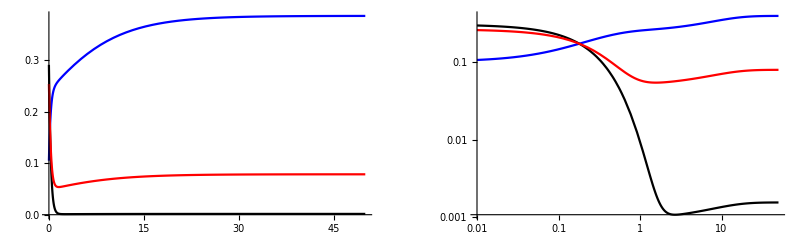

{{{0.386259,0.00155777}},{0.386354,0.0015582,0.0785174}}

```mathematica
tm=50;ρρ=0.2;ss=softP[ρρ,{1,2},{0.1,0.3},tm];
GraphicsRow[(#[{P1[t]/.ss,P2[t]/.ss,ρρ P1[t]+(1-ρρ)P2[t]/.ss},{t,0.01,tm},PlotStyle->{Blue,Black,Red}])&/@{Plot,LogLogPlot}]
{{P1[tm],P2[tm]}/.ss,{{1,0},{0,1},{ρρ,1-ρρ}}.softPeq[ρρ,{1,2.}]}
```

This simulates the version tracking allele frequencies.

```mathematica
K=100;Nm=0.1;s=0.01;L=100;pb=0.079;p=ConstantArray[pb,L];T=10^5;
Timing[nnp=runP[K,Nm,p,s,T];]
```

{231.595,Null}

The frequency in the rare habitat fluctuates around the predicted mean, and is close to the diffusion.

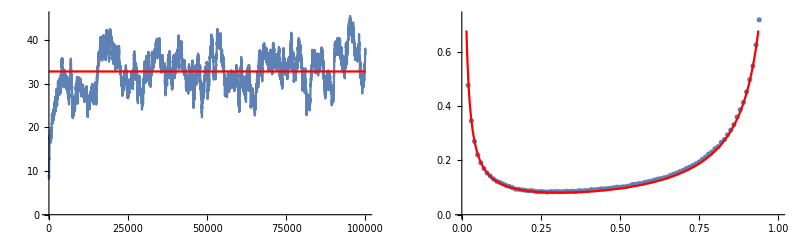

```mathematica
bc=BinCounts[Flatten[nnp⟦10^4;;-1⟧],{0,101}];
GraphicsRow[{Show[ListLinePlot[Transpose[{Range[0,T,10],Mean/@nnp⟦1;;-1;;10⟧}]],Plot[K mP[Nm,pb,K s],{t,0,T},PlotStyle->Red]],
Show[ListPlot[Transpose[{Range[0,1,1/K],bc/(T-10^4)}]],Plot[ψP[p,Nm,pb,K s],{p,0,1},PlotStyle->Red]]}]
```

#### Derivation of equilibrium under the diffusion approximation

Now, consider the full version, where allele frequencies are distributed according to the diffusion, There is an explicit formula for 𝔼[p], given p̄:

𝔼[p] = p̄(2 Nm p̄+12 Nm+12 Ks)/(2 Nm p̄2 Nm2 Ks)

If selection is equal and opposite, we can solve for p̄:

p̄ = p̄(ρ(2 Nm p̄+12 Nm+12 Ks)/(2 Nm p̄2 Nm2 Ks)+(1-ρ)(2 Nm p̄+12 Nm+1-2 Ks)/(2 Nm p̄2 Nm-2 Ks))

By setting  p̄=0 or 1, one can find the range of ρ for which polymorphism is possible. The hypergeometrics simplify to:

(1-g[-Ks_2])/(g[Ks_1]-g[-Ks_2])<ρ<  (g[Ks_2]-1)/(g[Ks_2]-g[-Ks_1])
where g[Ks]=(2 Nm p̄+12 Nm+12 Ks)/(2 Nm p̄2 Nm2 Ks)=2Nm (2 Ks_2)^(-2Nm)ⅇ^(2 Ks_2)Γ[2Nm,0,2 Ks_2]

This shows the critical ρ as a function of Ks (assuming symmetric selection ±s in the two habitats).  Nm=0.01,0.1,0.4,1,2 (black… red)

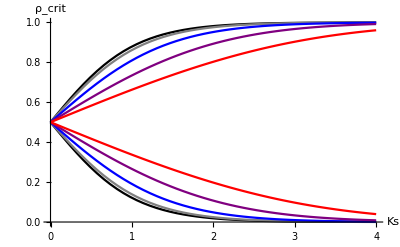

```mathematica
gr1[Nm_,c_]:=Plot[ρCrit[Nm,{Ks,Ks}],{Ks,0,4},AxesLabel->{"Ks","ρ_crit"},PlotStyle->c];
Show[MapThread[gr1,{{0.01,0.1,0.4,1,2},{Black,Gray,Blue,Purple,Red}}]]
```

Szep et al. give K s_crit=1/2 log[(1-ρ)/ρ]+Nm(1-2ρ).  This compares the prediction (black) with Ks (red). It seems to be accurate only for Ks<2:

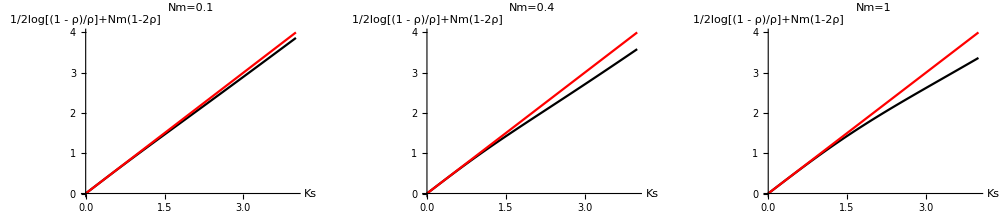

```mathematica
gr[Nm_]:=Plot[{1/2 Log[1/(ρCrit[Nm,{Ks,Ks}]⟦1⟧)-1]+Nm(1-2ρCrit[Nm,{Ks,Ks}]⟦1⟧),Ks},{Ks,0,4},PlotStyle->{Black,Red},AxesLabel->{"Ks","1/2log[(1 - ρ)/ρ]+Nm(1-2ρ]"},PlotLabel->("Nm="<>ToString[Nm])];
GraphicsRow[gr/@{0.1,0.4,1}]
```

#### Fig. 4 - response time for a single deme

This is derived using the transition matrix for a single deme. The codes that generated the figure are in the closed cells below (to open them,  click on cell → cell properties → open).

```mathematica
tt={#,respM[eqM[#,0.05,0.079,100],#,1,0.079,100,{2000,5}]}&/@{0.01,0.02,0.05,0.1,0.2,0.5,1,2,3,4,5,8};
tt1={#,respM[eqM[#,1,0.079,100],#,0.05,0.079,100,{2000,5}]}&/@{0.01,0.02,0.05,0.1,0.2,0.5,1,1.5,2,2.5,3,3.2,3.5,3.7,4,4.5,4.7,5,6,7,8,10};
int=Interpolation[tt];int1=Interpolation[tt1];
```

```mathematica
ttm=Join[{#,respM[eqM[0.1,#,0.079,100],1,#,0.079,100,{20000,10}]}&/@{0.01,0.02,0.03,0.05,0.07,0.1},{#,respM[eqM[0.1,#,0.079,100],1,#,0.079,100,{1000,1}]}&/@{0.15,0.2,0.25,0.3,0.5,0.7,1,1.5,2,3,5}];
ttm1=Join[{#,respM[eqM[1,#,0.079,100],0.1,#,0.079,100,{20000,10}]}&/@{0.01,0.02,0.03,0.05,0.07,0.1},{#,respM[eqM[1,#,0.079,100],0.1,#,0.079,100,{1000,1}]}&/@{0.15,0.2,0.25,0.3,0.5,0.7,1,1.5,2,3,5}];
```

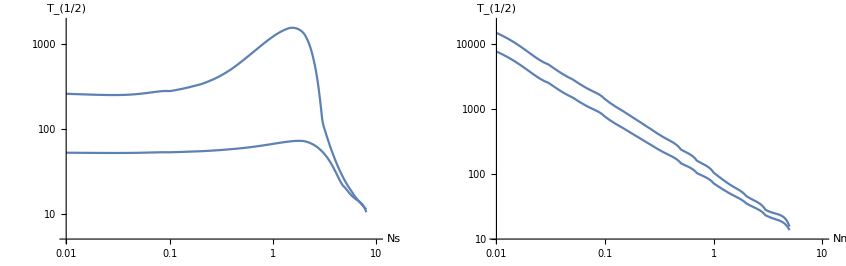

```mathematica
intm=Interpolation[ttm];
intm1=Interpolation[ttm1];
bs={FontFamily->"Times",FontSize->14};GraphicsRow[{Show[LogLogPlot[#[Ns],{Ns,0.01,8},Ticks->{{0.01,0.1,1,10},{10,100,1000}},PlotRange->{{0.01,10},{5,1800}}]&/@{int,int1},BaseStyle->bs,AxesLabel->{"Ns","T_(1/2)"}],
Show[LogLogPlot[intm[Nm],{Nm,0.01,5},Ticks->{{0.01,0.1,1,10},{10,100,1000,10^4}},PlotRange->{{0.01,10},{10,20800}}],LogLogPlot[intm1[Nm],{Nm,0.01,5},PlotRange->{{0.01,5},{5,20800}}],BaseStyle->bs,AxesLabel->{"Nm","T_(1/2)"}]}]
```

#### Derivation of the transition matrix

Loci are independent replicates, and so these should follow the predicted diffusion. Under the fixed-State approximation, a fraction P_1, P_2 are fixed for the + allele in the two habitats.   In any time interval, there is a pair {k_1,k_2} fixed for alleles within each of the two habitats, and we know the rate of change of the distribution:

(∂ψ)/(∂t)=λ_(1,-)((k_1+1)ψ[k_1+1,k_2]-k_1 ψ[k_1,k_2])+λ_(1,+)((n_1-k_1+1)ψ[k_1-1,k_2]-(n_1-k_1)ψ[k_1,k_2]) +terms for k_2

where the λ depend on the current mean, {k_1,k_2}.   This generates a set of equations for the ψ, but the dependence introduces a nonlinearity.  Loci may lose the focal allele by chance, in which case it cannot be recovered.  This leads to a downwards bias in the distribution.   One can  follow this process more easily for a single habitat, or for a rare habitat.

To try this approach numerically, we must include a low rate of mutation, so that there is a stationary state.  One would also like to find he  dynamics of the distribution of states, which can be done most simply by iterating a discrete-time version.

The rate of fixation of the P allele is (Nμ+Nm p̄)(2 s_1)/(1-ⅇ^(-2N s_1)), and of the Q allele: (Nμ+Nm q̄)(2 s_2)/(1-ⅇ^(-2N s_2)).  The rate is roughly m p̄, with no selection, so m sets the timescale. We need to index the elements by {k_1,k_2), each in the range {0,n_i}; and then calculate the matrix as a function of {k_1,k_2}.  This matrix then serves to iterate the process, or to generate stochastic realisations.

One could imagine (for a large # of loci) a diffusion approximation to this transition matrix.

#### Accuracy of the fixed-state approximation

We ran a simulation with ρ=0.2, s={0.02,-0.04}, K=50, Nm=0.02. The diffusion approximation predicts p̄=0.0723,  whereas the actual mean at the end was 0.0531. The fixed state prediction is 0.079, which is close to the diffusion. The codes that generated the figure are in the closed cells (to open them,  click on cell → cell properties → open).

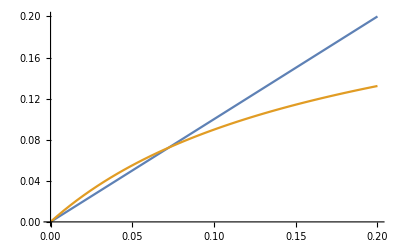

{0.053095,{pb→0.0723017},0.0785174}

```mathematica
Plot[{pb,0.2pbarS[50 0.02,0.02,pb]+0.8pbarS[-50 0.04,0.02,pb]},{pb,0,0.2}]
{Last[pbl],FindRoot[pb==0.2pbarS[50 0.02,0.02,pb]+0.8pbarS[-50 0.04,0.02,pb],{pb,0.05}],{0.2,0.8}.softPeq[0.2,50{0.02,0.04}]}
```

This is the distribution of allele counts for the last 50 time points, in rare and common habitats (left, right), averaged across loci. The two curves are the diffusion predictions, given the actual and predicted p̄ (orange: 0.053; red: 0.0723).  Both fit well, and the mass is

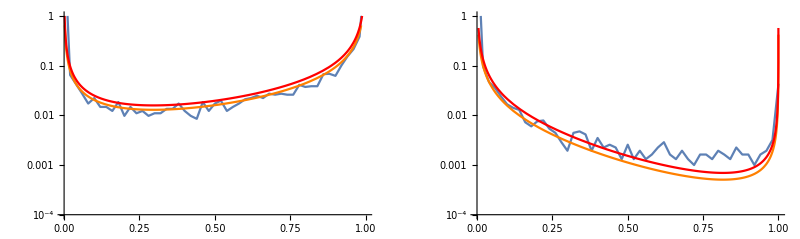

```mathematica
bc1=BinCounts[Flatten[jl2⟦-50;;-1,1;;20⟧],{0,51}];bc2=BinCounts[Flatten[jl2⟦-50;;-1,21;;100⟧],{0,51}];
GraphicsRow[{Show[ListLogPlot[Transpose[{Range[0,1,1/50],0.001+(50 bc1)/Total[bc1]}],Joined->True,PlotRange->{{0,1},{0.0001,1}}],
LogPlot[psiS[p,50 0.02,0.02,0.053],{p,0,1},PlotStyle->Orange],
LogPlot[psiS[p,50 0.02,0.02,0.0723],{p,0,1},PlotStyle->Red]],Show[ListLogPlot[Transpose[{Range[0,1,1/50],0.001+(50 bc2)/Total[bc2]}],Joined->True,PlotRange->{{0,1},{0.0001,1}}],LogPlot[psiS[p,-50 0.04,0.02,0.053],{p,0,1},PlotStyle->Orange],LogPlot[psiS[p,-50 0.04,0.02,0.0723],{p,0,1},PlotStyle->Red]]
}]
```

Figure.  The mean allele frequency in an infinite metapopulation, plotted against Nm; ρ=0.2,  N s_1, N s_2=1,-2 (lower curve) or 10,-20 (upper curve).  The fixed-state approximation, which applies for small Nm, is shown by the red lines.

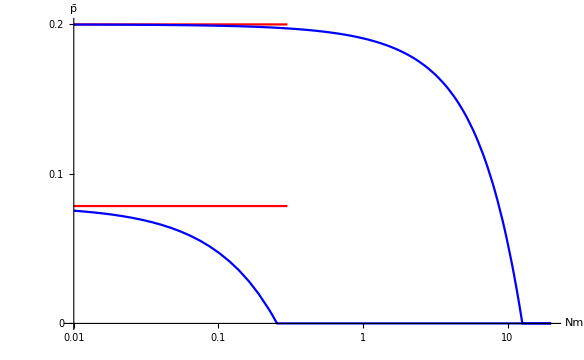

```mathematica
Show[LogLinearPlot[{{0.2,0.8}.softPeq[0.2,{1,2}],{0.2,0.8}.softPeq[0.2,{10,20}]},{Nm,0.01,0.3},PlotStyle->Red,Ticks->{Automatic,{0,0.1,0.2}},PlotRange->{{0.01,20},{0,0.2}}],
LogLinearPlot[{pbDiff[0.2,{1,2},Nm],pbDiff[0.2,{10,20},Nm],},{Nm,0.01,20},PlotStyle->Blue],AxesLabel->{"Nm","p̄"},BaseStyle->{FontFamily->"Times",FontSize->14}]
```

### Simulations

#### Example of a metapopulation: ρ=0.2, Ks=1,2, K=200, Nm=0.1

This sets up the simulation, running for 10^4 generations and storing every 100 generations.  The 10 loci evolve independently, and are in effect replicates.  This is reasonably fast (a few minutes)

```mathematica
nloci=10;KK=200;ndemes=100;ρρ=0.2;Nm=0.1;Tm=10000;δt=100;
sel={0.005,-0.01};s=initS[sel,ρρ,ndemes,nloci];
j0=initJ[KK,ρρ,ndemes,nloci];
time=0;jl=runPD[KK,Nm,s,{Tm,δt},j0];Dimensions[jl]
```

{101,100,10}

The top row shows the mean allele frequencies at 10 loci, and the overall mean (red), in the two habitats (left, right). The magenta curve shows the fixed state approximation, which underestimates the migration load.  The bottom row is similar, but shows the fraction of demes >50% instead of the mean allele frequency - which is closer to the  spirit of the fixed state approximation.  There is still a substantial discrepancy, though perhaps it is slightly smaller.

The codes that generated the figure are in the closed cells (to open them,  click on cell → cell properties → open) .

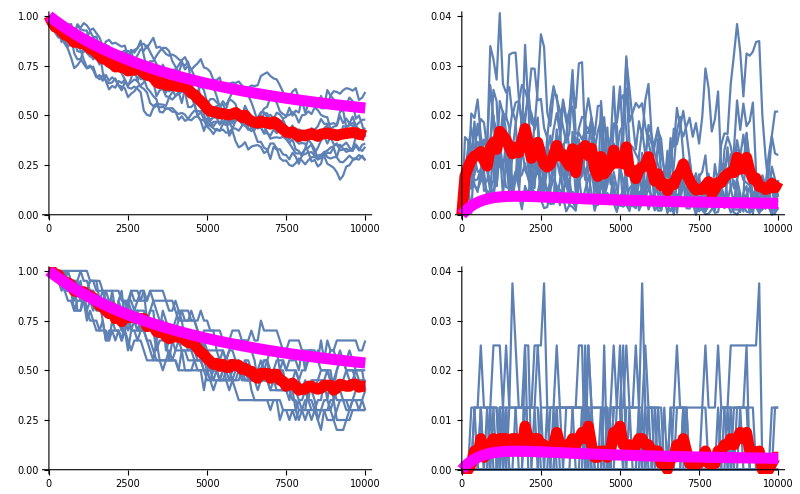

```mathematica
t=Tm/(KK/Nm);ss=softP[ρρ,Abs[KK sel],{1,0},Tm];
GraphicsGrid[{{Show[plotMeanP[KK,{Tm,δt},jl⟦All,1;;20⟧,{0,1}],
Plot[P1[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]],
Show[plotMeanP[KK,{Tm,δt},jl⟦All,-80;;-1⟧,{0,0.04}],
Plot[P2[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]]},
{Show[plotFixP[KK,{Tm,δt},jl⟦All,1;;20⟧,{0,1}],
Plot[P1[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]],
Show[plotFixP[KK,{Tm,δt},jl⟦All,-80;;-1⟧,{0,0.04}],
Plot[P2[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]]}}]
```

```mathematica
{{0.2,0.8}.softPeq[ρρ,KK Abs[sel]],Mean[Table[Mean[jl⟦-1,All,k⟧/KK],{k,10}]]//N}
```

{0.0785174,0.084805}

```mathematica
tm=Tm Nm/KK;ss=softP[ρρ,Abs[KK sel],{1,0},tm];
{0.2,0.8}.{P1[tm],P2[tm]}/.ss
```

{0.109205}

The overall p̄  fits the fixed-state prediction at equilibrium quite well, but .

The top row shows the individual allele frequency trajectories at 10 loci in one (arbitrarily chosen) deme, to get a sense of whether the fixed-state approximation is appropriate.  The trajectories do more or less make jumps between low & high frequency.  The bottom row shows the mean across all demes, which declines from the initial ρ=0.2, as the adaptive allele is lost from some fraction of demes in the rarer habitat.

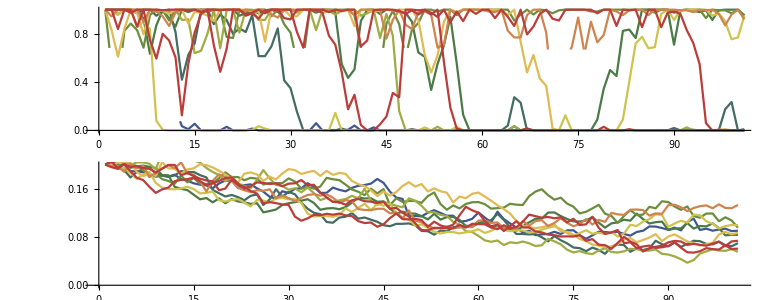

```mathematica
cf=ColorData["DarkRainbow"];
GraphicsColumn[{Show[Table[ListLinePlot[jl⟦All,1,k⟧/KK,PlotStyle->cf[k/nloci]],{k,nloci}],AspectRatio->0.2,PlotRange->{{0,100},{0,1}}],
Show[Table[ListLinePlot[Mean/@jl⟦All,All,k⟧/KK,PlotStyle->cf[k/nloci]],{k,nloci}],AspectRatio->0.2]}]
```

#### Example of a metapopulation: ρ=0.2, Ks={1,-2}, K=100, Nm=0.05

This sets up the simulation, running for 2 10^4 generations and storing every 100 generations.  The 10 loci evolve independently, and are in effect replicates.

```mathematica
nloci=10;KK=100;ndemes=100;ρρ=0.2;Nm=0.05;Tm=20000;δt=100;
sel={0.01,-0.02};s1=initS[sel,ρρ,ndemes,nloci];
j0=initJ[KK,ρρ,ndemes,nloci];
time=0;jl1=runPD[KK,Nm,s1,{Tm,δt},j0];Dimensions[jl1]
```

{201,100,10}

The top row shows the mean allele frequencies at 10 loci, and the overall mean (red), in the two habitats (left, right). The magenta curve shows the fixed state approximation, which underestimates the migration load.  The bottom row is similar, but shows the fraction of demes >50% instead of the mean allele frequency - which is closer to the  spirit of the fixed state approximation.  There is still a substantial discrepancy, though perhaps it is slightly smaller.

The codes that generated the figure are in the closed cells  (to open them,  click on cell → cell properties → open)

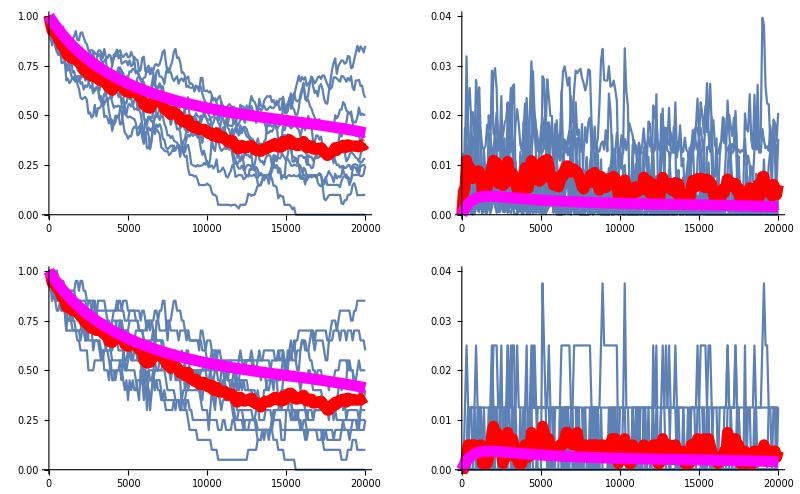

```mathematica
t=Tm/(KK/Nm);ss=softP[ρρ,Abs[KK sel],{1,0},tm];
GraphicsGrid[{{Show[plotMeanP[KK,{Tm,δt},jl1⟦All,1;;20⟧,{0,1}],
Plot[P1[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]],
Show[plotMeanP[KK,{Tm,δt},jl1⟦All,-80;;-1⟧,{0,0.04}],
Plot[P2[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]]},
{Show[plotFixP[KK,{Tm,δt},jl1⟦All,1;;20⟧,{0,1}],
Plot[P1[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]],
Show[plotFixP[KK,{Tm,δt},jl1⟦All,-80;;-1⟧,{0,0.04}],
Plot[P2[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{Thickness[0.02],Magenta}]]}}]
```

The top row shows the individual allele frequency trajectories at 10 loci in one (arbitrarily chosen) deme, to get a sense of whether the fixed-state approximation is appropriate.  The trajectories do more or less make jumps between low & high frequency.  The bottom row shows the mean across all demes, which declines from the initial ρ=0.2, as the adaptive allele is lost from some fraction of demes in the rarer habitat. The overall p̄  fits the fixed-state prediction quite well.

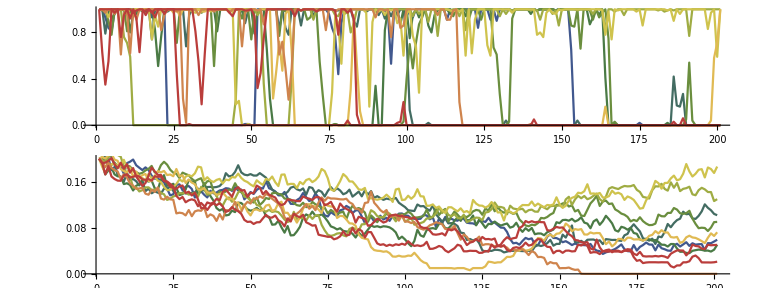

```mathematica
cf=ColorData["DarkRainbow"];
GraphicsColumn[{Show[Table[ListLinePlot[jl1⟦All,1,k⟧/KK,PlotStyle->cf[k/nloci]],{k,nloci}],AspectRatio->0.2,PlotRange->{{0,200},{0,1}}],
Show[Table[ListLinePlot[Mean/@jl1⟦All,All,k⟧/KK,PlotStyle->cf[k/nloci]],{k,nloci}],AspectRatio->0.2]}]
```

```mathematica
{{0.2,0.8}.softPeq[ρρ,KK Abs[sel]],Mean[Table[Mean[jl1⟦-1,All,k⟧/KK],{k,10}]]//N}
```

{0.0785174,0.07613}

#### Example of a metapopulation: ρ=0.2, Ks={1,-2}, K=50, Nm=0.02, 40 loci, 100 demes

This sets up the simulation, running for 5 10^4 generations and storing every 200 generations.  The 40 loci evolve independently, and are in effect replicates.

```mathematica
nloci=40;KK=50;ndemes=100;ρρ=0.2;Nm=0.02;Tm=50000;δt=200;
sel={0.02,-0.04};s1=initS[sel,ρρ,ndemes,nloci];
j0=initJ[KK,ρρ,ndemes,nloci];
time=0;jl2=runPD[KK,Nm,s1,{Tm,δt},j0];Dimensions[jl2]
```

$Aborted

```mathematica
Save["Metapops Jul 2021 jl2",jl2];
```

```mathematica
<<"Metapops Jul 2021 jl2";Dimensions[jl2]
```

{251,100,40}

The top row shows the mean allele frequencies at 40 loci, and the overall mean (red), in the two habitats (left, right). The magenta curve shows the fixed state approximation, which underestimates the migration load.  The bottom row is similar, but shows the fraction of demes >50% instead of the mean allele frequency - which is closer to the  spirit of the fixed state approximation.

The codes that generated the figure are in the closed cells below (to open them,  click on cell → cell properties → open)

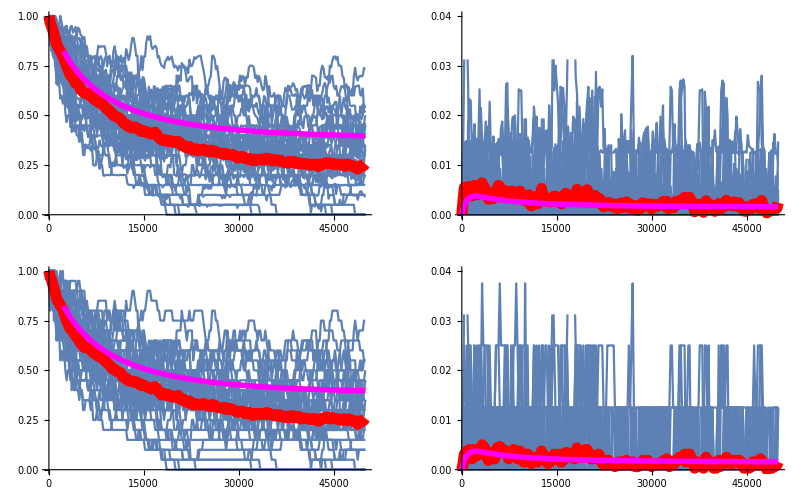

```mathematica
tm=Tm/(KK/Nm);ss=softP[ρρ,Abs[KK sel],{1,0},tm];thk=Thickness[0.01];
GraphicsGrid[{{Show[plotMeanP[KK,{Tm,δt},jl2⟦All,1;;20⟧,{0,1}],
Plot[P1[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{thk,Magenta}]],
Show[plotMeanP[KK,{Tm,δt},jl2⟦All,-80;;-1⟧,{0,0.04}],
Plot[P2[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{thk,Magenta}]]},
{Show[plotFixP[KK,{Tm,δt},jl2⟦All,1;;20⟧,{0,1}],
Plot[P1[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{thk,Magenta}]],
Show[plotFixP[KK,{Tm,δt},jl2⟦All,-80;;-1⟧,{0,0.04}],
Plot[P2[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{thk,Magenta}]]}}]
```

```mathematica
softP[ρρ,Abs[KK sel],{1,0},tm];{P1[tm],P2[tm]}/.ss
```

{{0.397012,0.00160709}}

There is still a substantial discrepancy,with both means of measurement.  Agreement is good for the common habitat, where the introgressing allele is rare (0.0024), but poor for the rare habitat, where it is at 0..256, compared with a prediction  of 0.397

The top row shows the individual allele frequency trajectories at 10 of the 40 loci in one (arbitrarily chosen) deme, to get a sense of whether the fixed-state approximation is appropriate.  The trajectories do more or less make jumps between low & high frequency.  The bottom row shows the mean across all demes, which declines from the initial ρ=0.2, as the adaptive allele is lost from some fraction of demes in the rarer habitat. However, there is considerable variation across loci, because of the concerted evolution across demes.  In the infinite-deme limit, there would be no such variability.

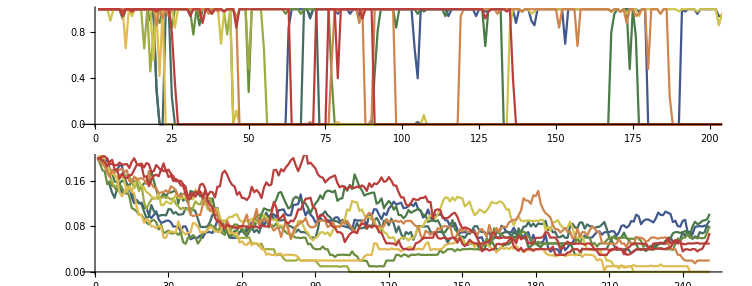

```mathematica
cf=ColorData["DarkRainbow"];
GraphicsColumn[{Show[Table[ListLinePlot[jl2⟦All,1,k⟧/KK,PlotStyle->cf[k/10]],{k,10}],AspectRatio->0.2,PlotRange->{{0,200},{0,1}}],
Show[Table[ListLinePlot[Mean/@jl2⟦All,All,k⟧/KK,PlotStyle->cf[k/10]],{k,10}],AspectRatio->0.2]}]
```

The overall mean in the metapopulation changes smoothly,  but converges to a substantially lower value than expected. The 10 individual loci follow markedly different paths, which may account for this variability:

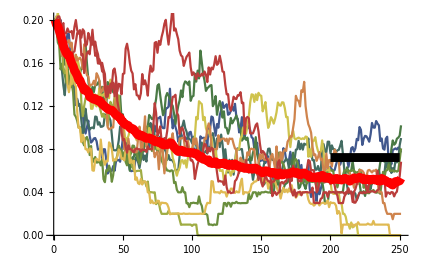

```mathematica
pbl=(Mean[Flatten[#]]/KK)&/@jl2//N;
Show[Table[ListLinePlot[(Mean[Flatten[#]]/KK)&/@jl2⟦All,All,k⟧//N,PlotStyle->cf[k/10]],{k,10}],ListLinePlot[pbl,PlotStyle->{Thickness[0.015],Red}],Plot[pbDiff[0.2,50{0.02,0.04},0.02],{t,200,250},PlotStyle->{Thickness[0.015],Black}]]
```

The observed and predicted mean frequencies are  close, and approaching the equilibrium, for the common habitat, but not the rare one:

```mathematica
pb=N[(#.Range[0,1,1/KK])/Total[#]]&/@{bc1,bc2};
{pb,{P1[tm],P2[tm]}/.ss⟦1⟧,softPeq[ρρ,Abs[KK sel]]}//TableForm
```

0.250858 | 0.00165588
0.397012 | 0.00160709
0.386354 | 0.0015582

### Fixed-state recursion with 10, 40 demes:

#### Setting up the transition matrix

There are 2151 rates in a 451×451 matrix, 𝒫:

```mathematica
Timing[ss=transM[{1,-1},0.001,0.05,{10,40}]]
```

{0.01966,SparseArray[…]}

#### Equilibrium vs Ns, μ/m

The top row of Figure X shows how the fraction of demes fixed at equilibrium depends on the strength of selection; the focal allele is favoured by N s_1 in 20% of demes (blue), and disfavoured by twice that (N s_2=-2N s_1) in 80% of demes. When mutation is appreciable (μ/m=0.05, top left), the allele is unlikely to be lost by chance, and so the equilibrium is insensitive to the number of demes, and close to the solution for an infinite population: results for 50, …,400, ∞ demes are superimposed, and almost indistinguishable. When selection is strong (right of each figure in the top row), all demes are fixed for the favoured allele, whereas when selection is weak, on average half of the demes are fixed for each allele. (Mutation is assumed symmetric).  In-between (0.1<Ns<1), the allele favoured in the rare habitat becomes rare, being pulled to low frequency by migration from the commoner habitat, where it is more strongly disfavoured.  When mutation is weak relative to selection, this pattern is exaggerated (μ/m=0.0005; top right).  Above a critical value, Ns_crit~0.8, polymorphism can be maintained by divergent selection, despite drift and gene flow. The equilibrium for an infinite population (purple) gives an upper bound, but stochastic loss from a finite set of demes reduces the expected frequency, and increases the critical N s_crit (dashed lines around Ns~1, for 50, 100,…  demes).  There is a wide region (0.03<N_s<1) where the allele is almost absent, being swamped by gene flow.  However, for very weak selection, the frequency of the allele increases towards the symmetric neutral equilibrium at 0.5.  (In this regime, the frequencies in the two habitats are almost identical, and cannot be distinguished in the figure).  In this regime (left of panels in the top row), although selection is negligible within demes (Ns<0.1), migration is much faster than mutation, and so selection over the whole metapopulation is effective in eliminating the allele that is deleterious in most demes.  When μ<<m, Ns<0.1 (left of top left panel), selection is more effective at the level of the whole metapopulation when there are more demes.

The bottom row of Fig. X shows the dependence on the relative rates of mutation versus migration, μ/m.   With high mutation rates, the equilibrium approaches a fraction 𝔼[k/n] =1/(1+ⅇ^(-2Ns)), with strong divergence when Ns_1=1 (right of bottom left panel), and weaker divergence when selection is weak (bottom right, N s_1=0.1).  With weak mutation and selection (left of bottom right panel), the allele that is less favoured overall is lost, independent of the number of demes (corresponding to the middle region of the upper right panel). WIth strong selection and weak mutation (left of bottom left panel), the allele favoured in the rare habitat can be fixed in nearly half the demes in an infinite metapopulation, but tends to be lost by chance from finite metapopulations, even with several hundred demes.

Figure X. The fraction of demes fixed in the two habitats (blue, red), as a function of selection strength (Ns,  top row) and the rate of mutation, relative to migration (μ/m, bottom row). The focal allele is favoured by selection N s_1 in 20% of demes (blue), and disfavoured by selection N s_2=-2N s_1 in 80% of demes.  In each plot, equilibria for 50, 100, 200 and 400 demes are superimposed (solid, dashed,… dotted lines), together with the limit for an infinite metapopulation (purple, orange).

The codes that generated the figure are in the closed cells below (to open them,  click on cell → cell properties → open)

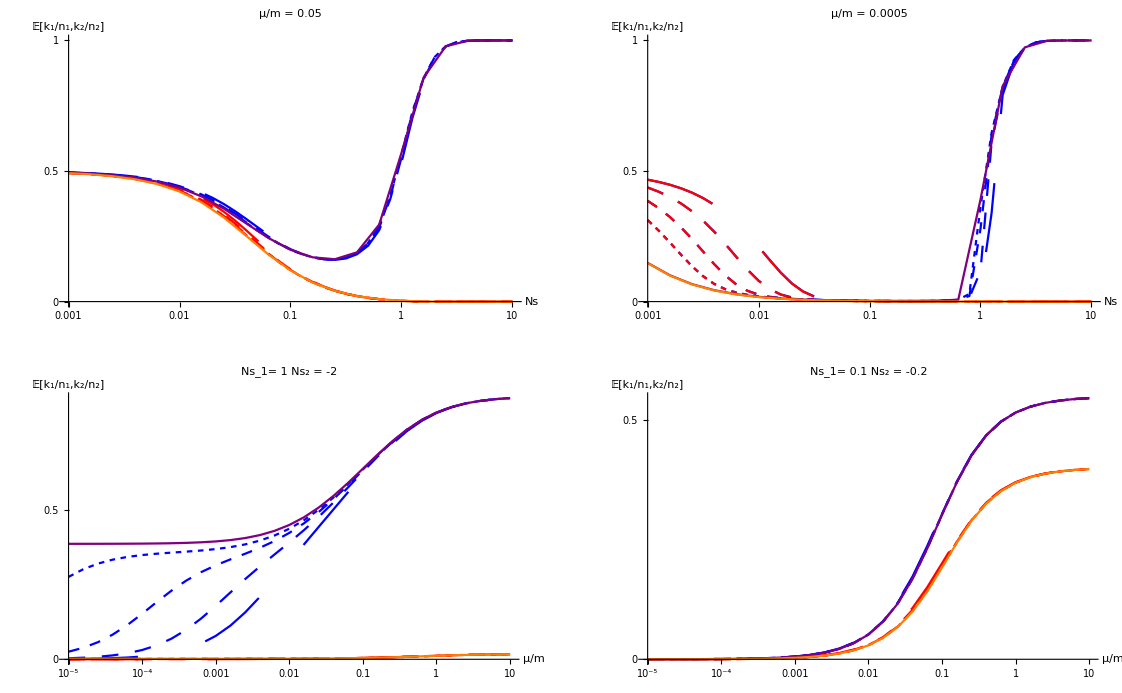

```mathematica
tbl[{Ns1_,Ns2_},{n1_,n2_}]:=tbl[{Ns1,Ns2},{n1,n2}]=
Flatten[{#,meanK[{n1,n2}][eqDist[{Ns1,Ns2},#,1,{n1,n2}]]/{n1,n2}}]&/@(10^Range[-5,1,0.2]);
tbl1[Nsr_,μm_,{n1_,n2_}]:=tbl1[Nsr,μm,{n1,n2}]=
Flatten[{#,meanK[{n1,n2}][eqDist[#{1,Nsr},μm,1,{n1,n2}]]/{n1,n2}}]&/@(10^Range[-3,1,0.1]);
tt[n_,{Ns1_,Ns2_},ρ_]:=tbl[{Ns1,Ns2},n{ρ,1-ρ}];tt1[n_,Nsr_,μm_,ρ_]:=tbl1[Nsr,μm,n{ρ,1-ρ}];
gr[{Ns1_,Ns2_},ρ_][n_Integer,d_]:=MapThread[ListLogLinearPlot[tt[n,{Ns1,Ns2},ρ]⟦All,{1,#1}⟧,Joined->True,PlotStyle->{#2,Dashing[d]},AxesOrigin->{10^-5,0},Ticks->{Automatic,{0,0.5,1}},AxesLabel->{"μ/m","𝔼[k_1/n_1,k_2/n_2]"},PlotLabel->"Ns_(1\)= "<>ToString[Ns1]<>" Ns_2 = "<>ToString[Ns2],BaseStyle->{FontFamily->"Times",FontSize->14}]&,{{2,3},{Blue,Red}}];
gr1[Nsr_,μm_,ρ_][n_Integer,d_]:=MapThread[ListLogLinearPlot[tt1[n,Nsr,μm,ρ]⟦All,{1,#1}⟧,Joined->True,PlotStyle->{#2,Dashing[d]},PlotRange->{{0.001,10},{0,1}},Ticks->{Automatic,{0,0.5,1}},AxesOrigin->{0.001,0},AxesLabel->{"Ns","𝔼[k_1/n_1,k_2/n_2]"},PlotLabel->"μ/m = "<>ToString[μm],BaseStyle->{FontFamily->"Times",FontSize->14}]&,{{2,3},{Blue,Red}}];
grT[{Ns1_,Ns2_},ρ_]:=Module[{tt,x},
tt=Flatten/@Table[{10^x,softPeq[10^x,ρ,{Ns1,Ns2}]},{x,-5,1,0.2}];
Show[ListLogLinearPlot[tt⟦All,{1,2}⟧,Joined->True,PlotStyle->Purple],
ListLogLinearPlot[tt⟦All,{1,3}⟧,Joined->True,PlotStyle->Orange]]];
grT1[Nsr_,μm_,ρ_]:=Module[{tt,x},
tt=Flatten/@Table[{10^x,softPeq[μm,ρ,10^x{1,Nsr}]},{x,-3,1,0.2}];
Show[ListLogLinearPlot[tt⟦All,{1,2}⟧,Joined->True,PlotStyle->Purple],
ListLogLinearPlot[tt⟦All,{1,3}⟧,Joined->True,PlotStyle->Orange]]];
nl={{50,100,200,400},{1,{0.03,0.03},{0.02,0.02},{0.01,0.01}}};
GraphicsGrid[{{Show[MapThread[gr1[-2,0.05,1/5],nl],grT1[-2,0.05,0.2]],
Show[MapThread[gr1[-2,0.0005,1/5],nl],grT1[-2,0.0005,0.2]]},
{Show[MapThread[gr[{1,-2},1/5],nl],grT[{1,-2},0.2]],
Show[MapThread[gr[0.1{1,-2},1/5],nl],grT[0.1{1,-2},0.2]]}}]
```

```mathematica
tbl[{Ns1_,Ns2_},{n1_,n2_}]:=tbl[{Ns1,Ns2},{n1,n2}]=
Flatten[{#,meanK[{n1,n2}][eqDist[{Ns1,Ns2},#,1,{n1,n2}]]/{n1,n2}}]&/@(10^Range[-5,1,0.5]);
tbl1[Nsr_,μm_,{n1_,n2_}]:=tbl1[Nsr,μm,{n1,n2}]=
Flatten[{#,meanK[{n1,n2}][eqDist[#{1,Nsr},μm,1,{n1,n2}]]/{n1,n2}}]&/@(10^Range[-3,1,1/5]);
tt[n_,{Ns1_,Ns2_},ρ_]:=tbl[{Ns1,Ns2},n{ρ,1-ρ}];tt1[n_,Nsr_,μm_,ρ_]:=tbl1[Nsr,μm,n{ρ,1-ρ}];
gr[{Ns1_,Ns2_},ρ_][n_Integer,d_]:=MapThread[ListLogLogPlot[tt[n,{Ns1,Ns2},ρ]⟦All,{1,#1}⟧,Joined->True,PlotStyle->{#2,Dashing[d]},AxesOrigin->{10^-5,0},PlotRange->{{0.001,10},{0.0001,1}},AxesLabel->{"μ/m","𝔼[k_1/n_1,k_2/n_2]"},PlotLabel->"Ns_1= "<>ToString[Ns1]<>" Ns_2 = "<>ToString[Ns2],BaseStyle->{FontFamily->"Times",FontSize->14}]&,{{2,3},{Blue,Red}}];
gr1[Nsr_,μm_,ρ_][n_Integer,d_]:=MapThread[ListLogLogPlot[tt1[n,Nsr,μm,ρ]⟦All,{1,#1}⟧,Joined->True,PlotStyle->{#2,Dashing[d]},PlotRange->{{0.001,10},{0.0001,1}},AxesOrigin->{0.001,0},AxesLabel->{"Ns","𝔼[k_1/n_1,k_2/n_2]"},PlotLabel->"μ/m = "<>ToString[μm],BaseStyle->{FontFamily->"Times",FontSize->14}]&,{{2,3},{Blue,Red}}];
nl={{50,100,200,400},{1,{0.03,0.03},{0.02,0.02},{0.01,0.01}}};
GraphicsGrid[{{Show[MapThread[gr1[-2,0.05,1/5],nl]],Show[MapThread[gr1[-2,0.0005,1/5],nl]]},{Show[MapThread[gr[{1,-2},1/5],nl],LogLogPlot[softPeq[0.2,{1,2}]⟦1⟧,{μm,10^-4,10^-3},PlotStyle->Black]],Show[MapThread[gr[0.1{1,-2},1/5],nl],LogLogPlot[softPeq[0.2,0.1{1,2}]⟦1⟧,{μm,10^-4,10^-3},PlotStyle->Black]]}}]
```

On a log-log scale, there are numerical difficulties for μ<<m, Ns>1

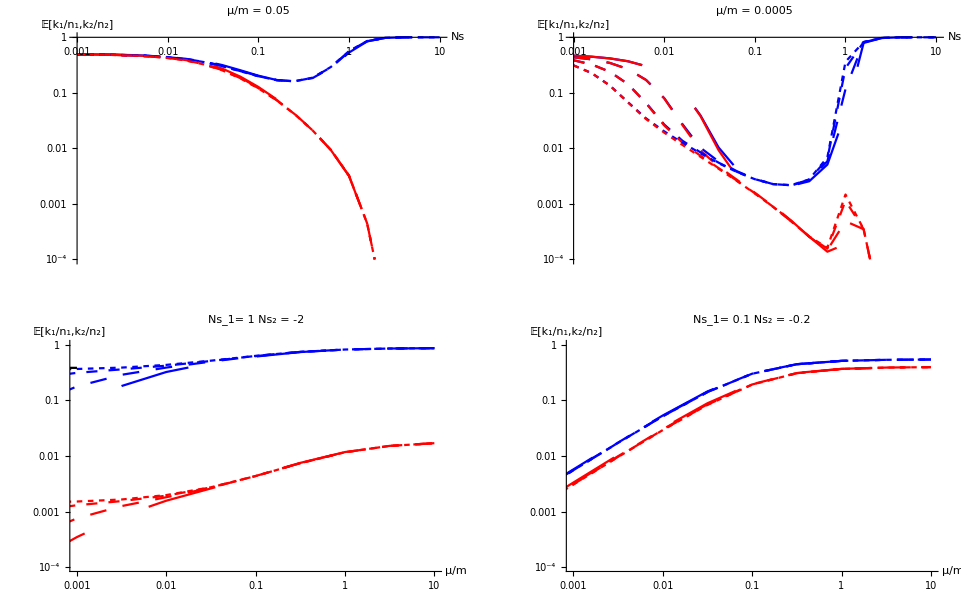

#### Change through time

We tabulate p_0,p_0.ⅇ^(5𝒫),…, giving the distribution at times 0,50N,…,10000N:

```mathematica
ss=transM[{1,-1},0.001,0.05,{10,40}];
me=MatrixExp[ 50 ss];
p0=ConstantArray[0,11×41];
{Timing[tb=NestList[#.me&,ReplacePart[p0,1->1],1000];],Timing[tb1=NestList[#.me&,ReplacePart[p0,index[{10,40}][{10,0}]->1],1000];]}
```

{{0.285971,Null},{0.215045,Null}}

Regardless of the starting point, the distribution converges to the stationary distribution:

```mathematica
yy=DeleteCases[Transpose[{index[{10,40}]/@Range[451],Chop[#,10^-3]&/@Last[tb],Chop[#,10^-3]&/@Last[tb1],Chop[es,10^-3]}],{_,0,0,0}]//Transpose;
TableForm[yy,TableDepth->2]
```

{0,0} | {0,1} | {1,0} | {1,1} | {1,2} | {2,0} | {2,1} | {2,2} | {3,0} | {3,1} | {3,2} | {3,3} | {4,0} | {4,1} | {4,2} | {4,3} | {4,4} | {5,0} | {5,1} | {5,2} | {5,3} | {5,4} | {6,0} | {6,1} | {6,2} | {6,3} | {6,4} | {7,0} | {7,1} | {7,2} | {7,3} | {7,4} | {7,5} | {8,0} | {8,1} | {8,2} | {8,3} | {8,4} | {9,0} | {9,1} | {9,2} | {9,3} | {9,4} | {10,0} | {10,1} | {10,2}
0.0293101 | 0.00317336 | 0.0433148 | 0.00957065 | 0.00157858 | 0.0587857 | 0.0198895 | 0.00446715 | 0.0723952 | 0.0333536 | 0.00956755 | 0.00218682 | 0.0796707 | 0.0468794 | 0.0164955 | 0.00449868 | 0.00104775 | 0.0767859 | 0.0554231 | 0.0232692 | 0.00742125 | 0.00199078 | 0.0630417 | 0.054293 | 0.026657 | 0.00979215 | 0.00298983 | 0.0423471 | 0.0426498 | 0.0241188 | 0.0100843 | 0.00347161 | 0.00104086 | 0.0218306 | 0.0253239 | 0.0163002 | 0.00768419 | 0.00295983 | 0.00768131 | 0.010142 | 0.00736039 | 0.00388232 | 0.00166266 | 0.00138433 | 0.00206084 | 0.00167343
0.0293101 | 0.00317336 | 0.0433148 | 0.00957065 | 0.00157858 | 0.0587857 | 0.0198895 | 0.00446715 | 0.0723952 | 0.0333536 | 0.00956755 | 0.00218682 | 0.0796707 | 0.0468794 | 0.0164955 | 0.00449868 | 0.00104775 | 0.0767859 | 0.0554231 | 0.0232692 | 0.00742125 | 0.00199078 | 0.0630417 | 0.054293 | 0.026657 | 0.00979215 | 0.00298983 | 0.0423471 | 0.0426498 | 0.0241188 | 0.0100843 | 0.00347161 | 0.00104086 | 0.0218306 | 0.0253239 | 0.0163002 | 0.00768419 | 0.00295983 | 0.00768131 | 0.010142 | 0.00736039 | 0.00388232 | 0.00166266 | 0.00138433 | 0.00206084 | 0.00167343
0.0293101 | 0.00317336 | 0.0433148 | 0.00957065 | 0.00157858 | 0.0587857 | 0.0198895 | 0.00446715 | 0.0723952 | 0.0333536 | 0.00956755 | 0.00218682 | 0.0796707 | 0.0468794 | 0.0164955 | 0.00449868 | 0.00104775 | 0.0767859 | 0.0554231 | 0.0232692 | 0.00742125 | 0.00199078 | 0.0630417 | 0.054293 | 0.026657 | 0.00979215 | 0.00298983 | 0.0423471 | 0.0426498 | 0.0241188 | 0.0100843 | 0.00347161 | 0.00104086 | 0.0218306 | 0.0253239 | 0.0163002 | 0.00768419 | 0.00295983 | 0.00768131 | 0.010142 | 0.00736039 | 0.00388232 | 0.00166266 | 0.00138433 | 0.00206084 | 0.00167343

```mathematica
xx=plotDist[tb⟦#+1⟧,{10,40},PlotRange->{{0,10},{0,5},{0,1000}}]&/@{100,300,1000};
GraphicsRow[xx]
```

-Graphics-

#### Example of a metapopulation: ρ=0.2, Ks={1,-2}, K=50, Nm=0.02, 40 loci, 100 demes

This sets up the simulation, running for 5 10^4 generations and storing every 200 generations.  The 40 loci evolve independently, and are in effect replicates.

```mathematica
nloci=40;KK=50;ndemes=100;ρρ=0.2;Nm=0.01;Tm=50000;δt=200;
sel={0.02,-0.04};s1=initS[sel,ρρ,ndemes,nloci];
j0=initJ[KK,ρρ,ndemes,nloci];
time=0;
jl2=runPD[KK,Nm,s1,{Tm,δt},j0];
Save["Metapops Jul 2021 Nm=0.01 jl2",jl2];
```

```mathematica
<<"Metapops Jul 2021 Nm=0.01 jl2";Dimensions[jl2]
```

{251,100,40}

This sets up the transition matrix approximation.

```mathematica
ss=transM[{1,-2},0,0.01,{20,80}];
me=MatrixExp[ 4 ss];
{Timing[tb=NestList[#.me&,ReplacePart[ConstantArray[0,21×81],index[{20,80}][{20,0}]->1],250];]}
```

{{3.17163,Null}}

```mathematica
nn=(meanK[{20,80}][#])/{20,80}&/@tb
```

{{1,0},{0.990111,0.000557794},{0.98047,0.00104336},{0.97107,0.00146525},{0.961901,0.00183104},{0.952955,0.00214744},{0.944224,0.00242036},{0.9357,0.00265505},{0.927377,0.00285612},{0.919246,0.00302768},{0.911302,0.00317333},{0.903538,0.00329627},{0.895948,0.0033993},{0.888527,0.00348492},{0.881267,0.00355531},{0.874165,0.0036124},{0.867215,0.00365789},{0.860413,0.00369328},{0.853753,0.00371988},{0.847231,0.00373885},{0.840843,0.00375121},{0.834585,0.00375786},{0.828452,0.00375958},{0.822442,0.00375705},{0.81655,0.00375089},{0.810772,0.00374161},{0.805107,0.00372969},{0.799549,0.00371552},{0.794097,0.00369946},{0.788747,0.00368181},{0.783497,0.00366286},{0.778343,0.00364282},{0.773283,0.00362191},{0.768315,0.00360029},{0.763436,0.00357813},{0.758643,0.00355556},{0.753934,0.00353268},{0.749308,0.0035096},{0.744762,0.00348641},{0.740293,0.00346317},{0.735901,0.00343995},{0.731582,0.00341679},{0.727336,0.00339376},{0.72316,0.00337088},{0.719053,0.00334818},{0.715013,0.00332569},{0.711038,0.00330344},{0.707127,0.00328144},{0.703278,0.0032597},{0.69949,0.00323824},{0.695761,0.00321706},{0.69209,0.00319618},{0.688476,0.00317559},{0.684917,0.0031553},{0.681412,0.00313531},{0.67796,0.00311562},{0.67456,0.00309624},{0.67121,0.00307715},{0.66791,0.00305836},{0.664658,0.00303987},{0.661453,0.00302166},{0.658294,0.00300374},{0.655181,0.00298611},{0.652112,0.00296875},{0.649086,0.00295167},{0.646103,0.00293486},{0.643161,0.00291832},{0.64026,0.00290203},{0.637399,0.002886},{0.634577,0.00287022},{0.631793,0.00285468},{0.629047,0.00283939},{0.626337,0.00282433},{0.623663,0.00280951},{0.621025,0.00279491},{0.618421,0.00278053},{0.615851,0.00276636},{0.613314,0.00275241},{0.61081,0.00273867},{0.608337,0.00272513},{0.605897,0.0027118},{0.603486,0.00269865},{0.601106,0.0026857},{0.598756,0.00267293},{0.596435,0.00266035},{0.594142,0.00264795},{0.591877,0.00263572},{0.58964,0.00262366},{0.58743,0.00261178},{0.585246,0.00260005},{0.583088,0.00258849},{0.580956,0.00257709},{0.578849,0.00256584},{0.576766,0.00255475},{0.574708,0.0025438},{0.572673,0.002533},{0.570662,0.00252234},{0.568674,0.00251182},{0.566709,0.00250144},{0.564765,0.0024912},{0.562844,0.00248108},{0.560944,0.0024711},{0.559065,0.00246124},{0.557206,0.00245151},{0.555369,0.0024419},{0.553551,0.00243241},{0.551753,0.00242304},{0.549974,0.00241378},{0.548214,0.00240464},{0.546473,0.00239561},{0.544751,0.00238668},{0.543047,0.00237787},{0.541361,0.00236916},{0.539692,0.00236055},{0.53804,0.00235205},{0.536406,0.00234364},{0.534788,0.00233533},{0.533187,0.00232712},{0.531602,0.002319},{0.530034,0.00231098},{0.52848,0.00230305},{0.526943,0.0022952},{0.525421,0.00228745},{0.523913,0.00227978},{0.522421,0.0022722},{0.520943,0.0022647},{0.51948,0.00225728},{0.51803,0.00224994},{0.516595,0.00224269},{0.515174,0.00223551},{0.513766,0.00222841},{0.512371,0.00222138},{0.510989,0.00221443},{0.509621,0.00220756},{0.508265,0.00220075},{0.506922,0.00219402},{0.505591,0.00218735},{0.504273,0.00218076},{0.502966,0.00217423},{0.501672,0.00216777},{0.500389,0.00216137},{0.499118,0.00215504},{0.497858,0.00214877},{0.496609,0.00214257},{0.495372,0.00213643},{0.494145,0.00213034},{0.492929,0.00212432},{0.491724,0.00211836},{0.49053,0.00211245},{0.489345,0.0021066},{0.488171,0.00210081},{0.487007,0.00209507},{0.485853,0.00208939},{0.484709,0.00208376},{0.483574,0.00207818},{0.482449,0.00207266},{0.481334,0.00206719},{0.480227,0.00206177},{0.47913,0.0020564},{0.478042,0.00205107},{0.476963,0.0020458},{0.475893,0.00204058},{0.474831,0.0020354},{0.473778,0.00203027},{0.472734,0.00202518},{0.471698,0.00202014},{0.47067,0.00201514},{0.469651,0.00201019},{0.468639,0.00200528},{0.467635,0.00200042},{0.46664,0.0019956},{0.465652,0.00199082},{0.464672,0.00198608},{0.463699,0.00198138},{0.462734,0.00197672},{0.461776,0.0019721},{0.460826,0.00196752},{0.459882,0.00196297},{0.458946,0.00195847},{0.458017,0.001954},{0.457095,0.00194957},{0.45618,0.00194518},{0.455272,0.00194082},{0.45437,0.0019365},{0.453475,0.00193221},{0.452586,0.00192796},{0.451704,0.00192374},{0.450829,0.00191956},{0.449959,0.00191541},{0.449096,0.00191129},{0.448239,0.0019072},{0.447389,0.00190315},{0.446544,0.00189913},{0.445705,0.00189514},{0.444873,0.00189118},{0.444046,0.00188725},{0.443224,0.00188335},{0.442409,0.00187948},{0.441599,0.00187564},{0.440795,0.00187183},{0.439996,0.00186805},{0.439203,0.0018643},{0.438415,0.00186057},{0.437632,0.00185687},{0.436855,0.0018532},{0.436082,0.00184956},{0.435316,0.00184594},{0.434554,0.00184235},{0.433797,0.00183879},{0.433045,0.00183525},{0.432298,0.00183174},{0.431556,0.00182825},{0.430819,0.00182479},{0.430086,0.00182135},{0.429359,0.00181793},{0.428636,0.00181455},{0.427917,0.00181118},{0.427203,0.00180784},{0.426494,0.00180452},{0.425789,0.00180122},{0.425089,0.00179795},{0.424393,0.0017947},{0.423701,0.00179147},{0.423014,0.00178826},{0.42233,0.00178507},{0.421651,0.00178191},{0.420977,0.00177877},{0.420306,0.00177565},{0.419639,0.00177255},{0.418977,0.00176947},{0.418318,0.00176641},{0.417664,0.00176337},{0.417013,0.00176035},{0.416366,0.00175734},{0.415723,0.00175436},{0.415084,0.0017514},{0.414448,0.00174846},{0.413816,0.00174554},{0.413188,0.00174263},{0.412564,0.00173974},{0.411943,0.00173687},{0.411326,0.00173402},{0.410712,0.00173119},{0.410101,0.00172837},{0.409495,0.00172558},{0.408891,0.0017228},{0.408291,0.00172003},{0.407695,0.00171729},{0.407101,0.00171456},{0.406511,0.00171184},{0.405925,0.00170915}}

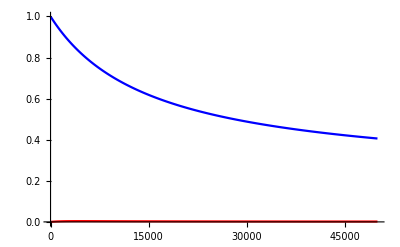

```mathematica
Show[MapThread[ListLinePlot[Transpose[{Range[0,50000,200],#1}],PlotStyle->#2]&,{Transpose[nn],{Blue,Red}}]]
```

```mathematica
Length[nn]
```

251

Figure xx.  Mean allele frequency through time, in the 20 demes where the focal allele is favoured (top), and the 80 demes where it is not (bottom). Thin lines show allele frequencies at 40 loci, averaged over demes; the red line shows the overall mean. The black curve shows the fixed state approximation.

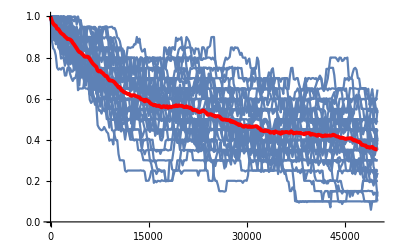

```mathematica
plotMeanP[KK,{Tm,δt},jl2⟦All,1;;20⟧,{0,1}]
```

The codes that generated the figure are in the closed cells below (to open them,  click on cell → cell properties → open).

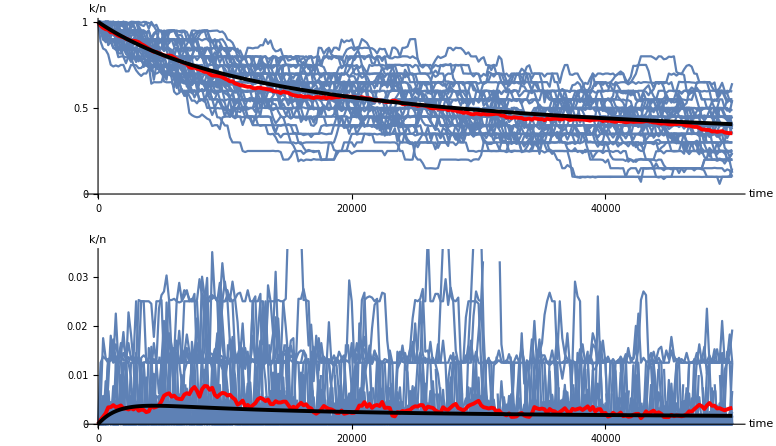

```mathematica
tm=Tm/(KK/Nm);ss=softP[ρρ,Abs[KK sel],{1,0},tm];
gr[j:(1|2)]:=Module[{dm,P,nd,pm,tk,thk=Thickness[0.007]},
dm=If[j==1,1;;20,-80;;-1];P=If[j==1,P1,P2];
nd=If[j==1,20,80];pm=If[j==1,1,0.035];tk={{0,20000,40000},If[j==1,{0,0.5,1},{0,0.01,0.02,0.03}]};
Show[plotMeanP[KK,{Tm,δt},jl2⟦All,dm⟧,{0,1}],
(*Plot[P[t/(KK/Nm)]/.ss,{t,0,Tm},PlotStyle->{thk,Magenta}],*)(* omit the infinite metapopulation prediction *)
ListLinePlot[Transpose[{Range[0,Tm,δt],tt⟦All,j⟧/nd}],PlotStyle->{thk,Black},BaseStyle->{FontFamily->"Times",FontSize->14}],Ticks->tk,AspectRatio->0.3,PlotRange->{{0,Tm},{0,pm}},AxesLabel->{"time","k/n"}]];
GraphicsColumn[{gr[1],gr[2]}]
```

The top row shows the individual allele frequency trajectories at 10 of the 40 loci in one (arbitrarily chosen) deme, to get a sense of whether the fixed-state approximation is appropriate.  The trajectories do more or less make jumps between low & high frequency.  The bottom row shows the mean across all demes, which declines from the initial ρ=0.2, as the adaptive allele is lost from some fraction of demes in the rarer habitat. However, there is considerable variation across loci, because of the concerted evolution across demes.  In the infinite-deme limit, there would be no such variability.

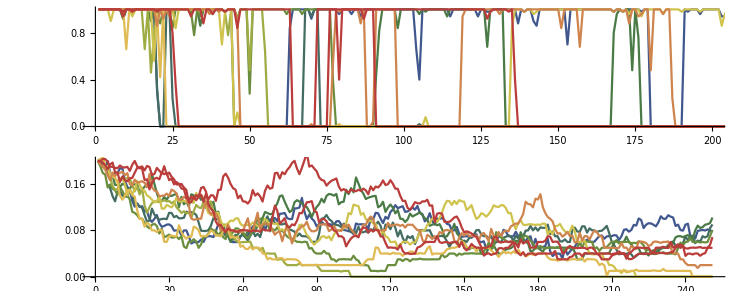

```mathematica
cf=ColorData["DarkRainbow"];
GraphicsColumn[{Show[Table[ListLinePlot[jl2⟦All,1,k⟧/KK,PlotStyle->cf[k/10]],{k,10}],AspectRatio->0.2,PlotRange->{{0,200},{0,1}}],
Show[Table[ListLinePlot[Mean/@jl2⟦All,All,k⟧/KK,PlotStyle->cf[k/10]],{k,10}],AspectRatio->0.2]}]
```

The overall mean in the metapopulation changes smoothly,  but converges to a substantially lower value than expected. The 10 individual loci follow markedly different paths, which may account for this variability:

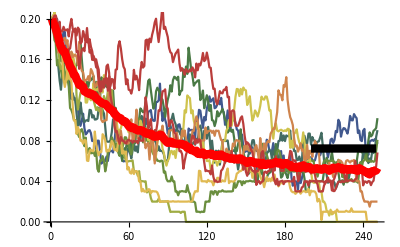

```mathematica
pbl=(Mean[Flatten[#]]/KK)&/@jl2//N;
Show[Table[ListLinePlot[(Mean[Flatten[#]]/KK)&/@jl2⟦All,All,k⟧//N,PlotStyle->cf[k/10]],{k,10}],ListLinePlot[pbl,PlotStyle->{Thickness[0.015],Red}],Plot[pbDiff[0.2,50{0.02,0.04},0.02],{t,200,250},PlotStyle->{Thickness[0.015],Black}]]
```

The observed and predicted mean frequencies are  close, and approaching the equilibrium, for the common habitat, but not the rare one:

```mathematica
pb=N[(#.Range[0,1,1/KK])/Total[#]]&/@{bc1,bc2};
{pb,{P1[tm],P2[tm]}/.ss⟦1⟧,softPeq[ρρ,Abs[KK sel]]}//TableForm
```

0.250858 | 0.00165588
0.397012 | 0.00160709
0.386354 | 0.0015582

## Definitions

### Simulations

#### alleleFreq

```mathematica
alleleFreq::usage="alleleFreq[{n,{j_1,…}]] gives the allele frequencies. Also applies to lists of populations.";
alleleFreq[{n_Integer,j_List}]:=If[n==0,Indeterminate,j/n];
alleleFreq[nj:{{_Integer,_List}...}]:=alleleFreq/@nj;
```

#### ψP, ψZ, mP, mPQ, mPr

```mathematica
ψP::usage="ψP[p,Nm,p̄,Ks] gives the density under the diffusion";
ψP[p_,Nm_,pb_,Ks_]:=p^(2Nm pb-1)(1-p)^(2Nm(1-pb)-1)ⅇ^(2Ks p)/ψZ[Nm,pb,Ks];
```

```mathematica
NIntegrate[p^(2Nm pb-1)(1-p)^(2Nm(1-pb)-1)ⅇ^(2Ks),{p,0,1}]
```

```mathematica
ψZ::usage="ψZ[Nm,p̄,Ks] gives the normalisation. ψZ[j,Nm,p̄,Ks] includes a factor p^j";
ψZ[Nm_,pb_,Ks_]:=ψZ[0,Nm,pb,Ks];
ψZ[j_,Nm_,pb_,Ks_]:=ψZ[j,Nm,pb,Ks]=Gamma[2 Nm (1-pb)] Gamma[j+2 Nm pb] Hypergeometric1F1Regularized[j+2 Nm pb,j+2 Nm,2 Ks];
```

```mathematica
mP::usage="mP[Nm,p̄,Ks] gives the mean allele frequency";
mP[Nm_,pb_,Ks_]:=ψZ[1,Nm,pb,Ks]/ψZ[0,Nm,pb,Ks];
```

```mathematica
mPQ::usage="mPQ[Nm,p̄,Ks] gives the mean pq";
mPQ[Nm_,pb_,Ks_]:=(ψZ[1,Nm,pb,Ks]-ψZ[2,Nm,pb,Ks])/ψZ[0,Nm,pb,Ks];
```

```mathematica
mPr::usage="mPr[Nm,p̄,Ks] gives the mean allele frequency, divided by p̄";
mPr[Nm_,pb_,Ks_]:=Hypergeometric1F1[1+2 Nm pb,1+2 Nm,2 Ks]/Hypergeometric1F1[2 Nm pb,2 Nm,2 Ks];
```

```mathematica
mQr::usage="mQr[Nm,p̄,Ks] gives the mean q, divided by q̄";
mQr[Nm_,pb_,Ks_]:=Hypergeometric1F1[1+2 Nm (1-pb),1+2 Nm,-2 Ks]/Hypergeometric1F1[2 Nm (1-pb),2 Nm,-2 Ks];
```

#### iterP, runP

```mathematica
iterP::usage="iterP[K,Nm,{p_1,…},s][{j_1,…}] iterates a population, assuming immigration rate Nm from a source with deleterious alleles at {p_1,…}, and fixed size K haploid individuals.";
iterP[K_,Nm_,p_List,s_][j_List]:=Module[{nm,jm,jj,j0=ConstantArray[0,Length[j]]},
time+=1;
nm=Min[K,RandomInteger[PoissonDistribution[Nm]]];
jm=If[nm==0,j0,RandomInteger[BinomialDistribution[nm,#]]&/@p];
jm+If[nm≥K,j0,RandomInteger[BinomialDistribution[K-nm,#]]&/@(j/(j+(K-j)ⅇ^-s))]];
```

I take a shortcut, ignoring LD. The algorithm draws the number of immigrants from a Poisson distribution, and then draws the # of copies of each allele for each class.  One needs to be careful to deal with the special case when either class goes extinct, to avoid division by zero.

```mathematica
runP::usage="runP[K,Nm,{p_1,…},s,T] applies iterP[K,m,{p_1,…},s] for T generations, starting at Kp";
runP[K_,Nm_,p_List,s_,T_Integer]:=(time=0;NestList[iterP[K,Nm,p,s],Round[K p],T]);
```

#### iterPD, runPD, makeMigrants

```mathematica
iterPD::usage="iterPD[K,Nm,{{s_(1, 1),…},…}][{{j_(1, 1),…},…}] iterates a population, assuming immigration rate Nm, taken from all demes at random, assuming fixed size K haploid individuals in all demes. Selection may vary across loci and across demes. ";
iterPD[K_,Nm_,s_List][j_List]:=Module[{nm,tnm,jm,jm1,pos,jj,j0,k,ndemes=Dimensions[j]⟦1⟧,nloci=Dimensions[j]⟦2⟧,pb=Mean[j]/K},
time+=1;
j0=ConstantArray[0,nloci];
nm=Min[K,#]&/@RandomInteger[PoissonDistribution[Nm],ndemes];
tnm=Tally[nm];
jm=makeMigrants[#,pb]&/@tnm;
jm1=ConstantArray[0,{ndemes,nloci}];
pos=Flatten[Position[nm,#⟦1⟧]]&/@tnm;
MapThread[(jm1⟦#1⟧=#2)&,{pos,jm}];
jm1+MapThread[Table[RandomInteger[BinomialDistribution[K-#1,#2⟦k⟧]],{k,nloci}]&,{nm,j/(j+(K-j)ⅇ^-s)}]];
```

```mathematica
makeMigrants::usage="makeMigrants[{n,k},{p_1,…}] makes k sets of genotypes for n migrants; returns a matrix k×n_loci, with each entry giving the number of P alleles, between 0 and n";
makeMigrants[{0,k_Integer},pb_List]:=ConstantArray[0,{k,Length[pb]}];
makeMigrants[{n_Integer,k_Integer},pb_List]:=
Transpose[RandomInteger[BinomialDistribution[n,#],k]&/@pb]
```

I take a shortcut, ignoring LD. The algorithm draws the number of immigrants from a Poisson distribution, and then draws the # of copies of each allele for each class.  One needs to be careful to deal with the special case when either class goes extinct, to avoid division by zero.

```mathematica
runPD::usage="runPD[K,Nm,{{s_(1, 1),…},…},T,{{j_(1, 1),…},…}] applies iterPD[K,Nm,s] for T generations. Selection may vary across loci and across demes. runPD[K,Nm,{{s_(1, 1),…},…},{T,δt},{{j_(1, 1),…},…}] stores results at intervals δt";
runPD[K_,Nm_,s_,T_Integer,j0_List]:=NestList[iterPD[K,Nm,s],j0,T];
runPD[K_,Nm_,s_,{T_Integer,δ_Integer},j0_List]:=(time=0;NestList[Last[runPD[K,Nm,s,δ,#]]&,j0,Quotient[T,δ]]);
```

#### initS, initJ

```mathematica
initS::usage="initS[{s_0,s_1},ρ,n_demes,n_loci] sets up an array of selection coefficients, where the first nρ demes have s_0, and the remaning n(1-ρ) have s_1";
initS[{s0_,s1_},ρ_,nd_Integer,nl_Integer]:=Join[ConstantArray[s0,{Round[nd ρ],nl}],ConstantArray[s1,{Round[nd(1- ρρ)],nl}]];
```

```mathematica
initJ::usage="initJ[K,ρ,n_demes,n_loci] sets up an array of initial j_(i, k), with perfect adaptation. The first nρ demes are fixed for one allele, and the remaning n(1-ρ) for the other";
initJ[K_,ρ_,nd_Integer,nl_Integer]:=Join[ConstantArray[K,{Round[nd ρ],nl}],ConstantArray[0,{Round[nd (1-ρ)],nl}]];
```

#### plotMeanP, plotFixP,frac

```mathematica
plotMeanP::usage="plotMeanP[K,{T_max,δt},{{{j_(t, d, l)…},…},…},{p_min,p_max}] plots the mean p at all loci, using the specified range of allele frequencies";
plotMeanP[K_,{Tm_Integer,δt_Integer},jl_List,pr_,opts___Rule]:=Module[{pp=(Mean/@jl)/K,rn=Range[0,Tm,δt]},
Show[ListLinePlot[Transpose[{rn,#/K}],opts]&/@Transpose[Mean/@jl],
ListLinePlot[Transpose[{rn,Mean/@pp}],PlotStyle->{Thickness[0.007],Red}],
PlotRange->{{0,Tm},pr},AxesOrigin->{0,0}]];
```

```mathematica
plotFixP::usage="plotFixP[K,{T_max,δt},{{{j_(t, d, l)…},…},…},{p_min,p_max}] plots the fraction of demes>50% at all loci, using the specified range of allele frequencies";
plotFixP[K_,{Tm_Integer,δt_Integer},jl_List,pr_]:=Module[{rn=Range[0,Tm,δt],loc,nloci=Length[jl⟦1,1⟧]},
Show[Table[ListLinePlot[Transpose[{rn,frac[K/2]/@jl⟦All,All,loc⟧}]],{loc,nloci}],
ListLinePlot[Transpose[{rn,Mean[Table[frac[K/2]/@jl⟦All,All,loc⟧,{loc,nloci}]]}],PlotStyle->{Thickness[0.02],Red}],
PlotRange->{{0,Tm},pr},AxesOrigin->{0,0}]];
```

```mathematica
frac::usage="frac[j^*][{j_1,…}] gives the fraction of the j_i larger than j^*";
frac[j_][jl_List]:=Length[Select[jl,#>j&]]/Length[jl];
```

#### iterNP, runNP

```mathematica
iterNP::usage="iterNP[r,K,Nm,{p_1,…},s][{N,{j_1,…}}] iterates a population, assuming immigration rate Nm from a source with deleterious alleles at {p_1,…}. iterNP[r,K,Nm,{s_1,…}][{N_1,{j_(1, 1),…}…}] iterates a metapopulation; s is the selection in each deme, assumed the same for all loci.";
iterNP[r_,K_,Nm_,p_List,s_][{n_,j_List}]:=Module[{nn,nm,jm,jj,L=Length[j],j0},
time+=1;
j0=ConstantArray[0,L];
nm=RandomInteger[PoissonDistribution[Nm]];
jm=If[nm==0,j0,RandomInteger[BinomialDistribution[nm,#]]&/@p];
nn=If[n==0,0,RandomInteger[PoissonDistribution[n Exp[r(1-n/K)+ s Total[j]/n-If[s>0,s L,0]]]]];
jj=If[nn==0,j0,
RandomInteger[BinomialDistribution[nn,#]]&/@(j/((n-j)ⅇ^-s+j))];
{nm+nn,jm+jj}];
```

```mathematica
iterNP[r_,K_,Nm_,s_List][pop:{{_Integer,_List}...}]:=Module[{jb,nb,t0,np},
t0=time;
jb=Mean[pop⟦All,2⟧];nb=Mean[pop⟦All,1⟧];
np=MapThread[If[#1⟦1⟧==0,{0,ConstantArray[0,Length[#1⟦2⟧]]},
iterNP[r,K,Nm nb/K,jb/nb,#2][#1]]&,{pop,s}];
time=t0+1;np];
```

I take a shortcut, ignoring LD. The algorithm draws the number of immigrants, and the number of natives, from separate Poisson distributions, and then draws the # of copies of each allele for each class.  One needs to be careful to deal with the special case when either class goes extinct, to avoid division by zero.

```mathematica
runNP::usage="runNP[r,K,Nm,{p_1,…},s,T][{N,{j_1,…}}] applies iterNP[r,K,Nm,{p_1,…},s] for T generations. runNP[r,K,Nm,L,{s_1,…},T] applies iterNP[r,K,Nm,{s_1,…}], starting with perfect adaptation. Using {T,δT} stores results only at intervals δT.";
runNP[r_,K_,Nm_,p_List,s_,T_Integer][{n_Integer,j_List}]:=
Module[{},time1+=T;NestList[iterNP[r,K,Nm,p,s],{n,j},T]];
runNP[r_,K_,Nm_,p_List,s_,{T_Integer,δ_Integer}][{n_Integer,j_List}]:=
runNP[r,K,Nm,p,s,{T,δ}][{n,j}]=Module[{},
time1=0;NestList[Last[runNP[r,K,Nm,p,s,δ][#]]&,{n,j},Round[T/δ]]];
runNP[r_,K_,Nm_,L_Integer,s_,T_Integer][nj:{{_Integer,_List}...}]:=Module[{},time1+=T;NestList[iterNP[r,K,Nm,s],nj,T]];
runNP[r_,K_,Nm_,L_Integer,s_,{T_Integer,δ_Integer}][nj:{{_Integer,_List}...}]:=
runNP[r,K,Nm,L,s,{T,δ}][nj]=Module[{np},
time1=0;NestList[Last[runNP[r,K,Nm,L,s,δ][#]]&,nj,Round[T/δ]]];
```

#### load

```mathematica
load::usage="load[{n,{j_1,…}] calculates the total allele frequency, summed over loci, returning Indeterminate if n=0. Also applies to lists of populations.";
load[{0,_List}]:=Indeterminate;
load[{n_Integer,j_List}]:=Total[j]/n;
load[pop:{{_Integer,_List}...}]:=load/@pop;
```

#### substRate

```mathematica
substRate::usage="substRate[Ns,Nμ,Nm,p̂] gives the substitution rate to this allele, relative to 2s. substRate[-Ns,Nμ,Nm,1-p̂] gives the rate of loss. ";
substRate[Ns_,Nμ_,Nm_,pb_]:=(Nμ+Nm pb)/(1-Exp[-2Ns]);
```

#### index

```mathematica
index::usage="index[{n_1,n_2}][{k_1,k_2}] generates an integer 1…(n_1+1)×(n_2+1) that represents the pair {k_1,k_2}. index[{n_1,n_2}][i] inverts this to recover the original pair.";
index[{n1_Integer,n2_Integer}][{k1_Integer,k2_Integer}]:=1+k2+(n2+1)k1;
index[{n1_Integer,n2_Integer}][i_Integer]:=QuotientRemainder[i-1,n2+1];
```

#### transM

```mathematica
transM::usage="transM[{Ns_1,Ns_2},Nμ,Nm,{n_1,n_2}] gives the transition matrix for two habitats with selection Ns_1,Ns_2. Scaled relative to N generations. transM[{N_1,N_2},{s_1,s_2},μ,Nm,{n_1,n_2}] is scaled in generations, and allows for different population sizes in the two habitats.";
transM[{Ns1_,Ns2_},Nμ_,Nm_,{n1_Integer,n2_Integer}]:=transM[{1,1},{Ns1,Ns2},Nμ,Nm,{n1,n2}];
transM[{N1_,N2_},{s1_,s2_},μ_,m_,{n1_Integer,n2_Integer}]:=
Module[{pb,Nb,f=index[{n1,n2}],λ1up,λ1down,λ2up,λ2down,nt=(n1+1)(n2+1),k1,k2,rls,f0},
rls=Flatten[Table[f0=f[{k1,k2}];pb=(k1+k2)/(n1+n2);Nb=(n1 N1+n2 N2)/(n1+n2);
λ1up=2s1 substRate[N1 s1, N1 μ, Nb m,pb];λ1down=-2s1 substRate[-N1 s1,N1 μ,Nb m,1-pb];
λ2up=2 s2 substRate[N2 s2, N1 μ,Nb m,pb];λ2down=-2 s2 substRate[-N2 s2,N2 μ,Nb m,1-pb];
{{f0,f0}->-λ1down k1-λ1up(n1-k1)-λ2down k2-λ2up(n2-k2),
{f0,f[{k1+1,k2}]}->λ1up (n1-k1) ,{f0,f[{k1-1,k2}]}->λ1down k1,
{f0,f[{k1,k2+1}]}->λ2up (n2-k2) ,{f0,f[{k1,k2-1}]}->λ2down k2},
{k2,0,n2},{k1,0,n1}],2];
SparseArray[DeleteCases[rls,_->(0|0.)],{nt,nt}]];
```

Note that the rate of fixation is (2s(Nμ+Nm p̄))/(1-Exp[-2Ns]), and the number of migrants coming in is  (ρ N_1+(1-ρ)N_2)m. In the soft selection case, where N_1=N_2=K, this simplifies to Km.

#### npred

```mathematica
nPred::usage="nPred[{n_1,n_2},L,{S_1,S_2}][{p_0,…}] gives the predicted {N_1,N_2}/K, given L loci which follow a distribution of states {p_0,…}.";
nPred[{n1_,n2_},L_,{S1_,S2_}][p_List]:=Module[{mn=meanK[{n1,n2}][p]},
Max[0,#]&/@(1-L{1-mn⟦1⟧/n1,mn⟦2⟧/n2}{S1,-S2})];
```

#### runM

```mathematica
runM::usage="runM[r_0,K,Nm,L,{s_1,s_2},{n_1,n_2},{T_m,δt}] stores the semi-deterministic approximation using a transition matrix.";
runM[r0_,K_,Nm_,L_,{s1_,s2_},{n1_Integer,n2_Integer},{Tm_,δt_}]:=
runM[r0,K,Nm,L,{s1,s2},{n1,n2},{Tm,δt}]=Module[{nn,p0=ReplacePart[ConstantArray[0,(n1+1)(n2+1)],index[{n1,n2}][{n1,0}]->1]},
NestList[(time+=δt;nn=nPred[{n1,n2},L,{s1,s2}/r0][#];#.MatrixExp[ δt transM[K nn,{s1,s2},0,Nm/K,{n1,n2}]])&,p0,Round[Tm/δt]]];
```

#### trim

```mathematica
trim::usage="trim[{p_1,…}] sets negative values to zero and renormalises.";
trim[p_List]:=Module[{np},
np=Max[0,#]&/@p;
np/Total[np]];
```

#### plotDist

```mathematica
plotDist::usage="plotDist[{p_(0, 0),…},{n_1,n_2}] plots a 3D histogram.";
plotDist[p_List,{n1_Integer,n2_Integer},opts___Rule]:=Module[{nt=(n1+1)(n2+1),tt,tts,k=1000,scale},
tt=DeleteCases[Transpose[{index[{n1,n2}]/@Range[nt],Chop[#,10^-6]&/@p}],{_,0}];
scale=Round[k/Max[Last/@tt]];
tts=Flatten[tt/.{{i_,j_},x_}:>ConstantArray[{i,j},Round[scale x]],1];
Histogram3D[tts,opts,PlotRange->{{0,n1},{0,n2},{0,1.1k}}]];
```

#### eqDist

```mathematica
eqDist::usage="eqDist[𝒫,{n_1,n_2}] or eqDist[{Ns_1,Ns_2},Nμ,Nm,{n_1,n_2}] gives the stationary distribution";
eqDist[𝒫_SparseArray,{n1_Integer,n2_Integer}]:=Module[{es=Eigenvectors[Transpose[𝒫],-1]⟦1⟧//Chop},es/Total[es]];
eqDist[{Ns1_,Ns2_},Nμ_,Nm_,{n1_Integer,n2_Integer}]:=eqDist[transM[{Ns1,Ns2},Nμ,Nm,{n1,n2}],{n1,n2}];
```

#### meanK

```mathematica
meanK::usage="meanK[{n_1,n_2}][{p_0,…}] gives the mean # of demes fixed in the two habitats";
meanK[{n1_Integer,n2_Integer}][p_List]:=Module[{pt=index[{n1,n2}]/@Range[(n1+1)(n2+1)]},
p.pt];
```

### Graphics

#### xyt

```mathematica
xyt::usage="xyt[j] lists the coordinates of an j×j grid,in the form {{1,1},{1,2},…,{j,j}}. Placing->Random gives random locations; Placing->Circle gives (n-1)(2n+1) placements within a circle.";
Options[xyt]={Placing->Grid};
xyt[n_Integer,opts___Rule]:=Module[{ϵ,δ,θ,r,i,j,pflg=Placing/.{opts}/.Options[xyt]},
Switch[pflg,
Random,RandomReal[{0,n},{n^2,2}],
Grid,Flatten[Table[{i,j},{i,1,n},{j,1,n}],1],
Circle,Flatten[Table[δ=(2π)/(1+4r);ϵ=RandomReal[{0,δ}];Table[r{Cos[θ],Sin[θ]},{θ,ϵ,ϵ+2π-δ,δ}],{r,0,n-1}],1],
_,$Failed]];
```

#### pick

```mathematica
pick::usage="pick[n,j] stores a list of j evenly spaced points in {1…n}";
pick[n_Integer,j_Integer]:=pick[n,j]=Drop[Range[1,n,Quotient[n,j]],-1];
```

#### makeDisks

```mathematica
makeDisks::usage="makeDisks[{{n_1,{p_(1, 1),…}},k] makes a k×k grid of disks, with radius √N, and hue indicating load; by default, blue->red as load increases. Random->True gives a random placement of k^2 disks in k×k. ColorFunction->cf sets a function to represent the load (cf[1] for load 0, cf[0] for max load; default ColorData[RedBlueTones]). DiskSpacing scales distance between disks (default 20) and DiskHue→γ scales the colour as cf[1-load) (default 0.5)  ";
Options[makeDisks]={DiskHue->0.5,DiskSpacing->20,ColorFunction->ColorData["RedBlueTones"]};
makeDisks[nnp_List,k_Integer,opts___Rule]:=Module[{nnps,xy,
cf=ColorFunction/.{opts}/.Options[makeDisks],
Δ=DiskSpacing/.{opts}/.Options[makeDisks],
γ=DiskHue/.{opts}/.Options[makeDisks]},
xy=xyt[k,opts];nnps=nnp⟦pick[Length[nnp],Length[xy]]⟧;
Graphics[MapThread[{cf[#3],Disk[#1,#2]}&,{Δ xy,√nnps⟦All,1⟧,(1- γ load[nnps])/.Indeterminate->0}]]];
```

### Diffusion approximation

#### psiS

```mathematica
psiS::usage="psiS[p,Ns,Nm,pb] gives the diffusion prediction. psiS[Ns,Nm,pb] gives the normalisation";
psiS[p_,Ns_,Nm_,pb_]:=p^(2Nm pb-1)(1-p)^(2Nm(1-pb)-1)Exp[2Ns p]/psiS[Ns,Nm,pb];
psiS[Ns_,Nm_,pb_]:=Gamma[2 Nm (1-pb)] Gamma[2 Nm pb] Hypergeometric1F1Regularized[2 Nm pb,2 Nm,2 Ns];
```

#### pbarS

```mathematica
pbarS::usage="pbarS[Ns,Nm,pb] gives the mean frequency under the diffusion";
pbarS[Ns_,Nm_,pb_]:=(pb Hypergeometric1F1[1+2 Nm pb,1+2 Nm,2 Ns])/Hypergeometric1F1[2 Nm pb,2 Nm,2 Ns];
```

#### pbDiff

```mathematica
pbDiff::usage="pbDiff[ρ,{Ns_1,Ns_2},Nm] predicts the equilibrium under the diffusion approximation";
pbDiff[ρ_,{Ns1_,Ns2_},Nm_]:=Module[{pb},
pb/.FindRoot[pb==ρ pbarS[Ns1,Nm,pb]+(1-ρ)pbarS[-Ns2,Nm,pb],{pb,0.05}]];
```

#### psiN

```mathematica
psiN::usage="psiN[N,ζ,M] gives the distribution of N under the diffusion. psiN[N,ζ,M,{(p̄)_1,…},S] includes selection on L loci. psiN[N,ζ,M,p̄,S,L] assumes symmetry";
psiN[n_,ζ_,M_]:=n^(2ζ M-1)Exp[-ζ (1-n)^2]/Z[ζ,M];
psiN[n_,ζ_,M_,p_List,S_]:=n^(2ζ M-1)Exp[-ζ (1-n)^2](Times@@(int[n,ζ M,#,ζ S]&/@p))/Z[ζ,M,p,S];
psiN[n_,ζ_,M_,p_,S_,L_Integer]:=n^(2ζ M-1)Exp[-ζ (1-n)^2]int[n,ζ M,p,ζ S]^L/Z[ζ,M,p,S,L];
```

#### meanN, meanNP

```mathematica
meanN::usage="meanN[ζ,M] gives the mean N under the diffusion. psiN[ζ,M,S,{(p̄)_1,…}] includes selection on L loci. meanN[ζ,M,S,p̄,L] assumes symmetry";
meanN[ζ_,M_]:=Z[ζ,M+1/(2ζ)]/Z[ζ,M];
meanN[ζ_,M_,p_List,S_]:=Module[{n},
NIntegrate[n^(2ζ M)Exp[-ζ (1-n)^2](Times@@(int[n,ζ M,#,ζ S]&/@p)),{n,0,∞}]/Z[ζ,M,p,S]];
meanN[ζ_,M_,p_,S_,L_Integer]:=Module[{n},
NIntegrate[n^(2ζ M)Exp[-ζ (1-n)^2] int[n,ζ M,p,ζ S]^L,{n,0,∞}]/Z[ζ,M,p,S,L]];
```

```mathematica
meanNP::usage="meanNP[ζ,M,{(p̄)_1,…},S,i] gives the mean N p_i under the diffusion. meanNP[ζ,M,p̄,S,L] assumes symmetry. meanNP[N,ζ,M,{(p̄)_1,…},S,i], meanNP[N,ζ,M,p̄,S,L] give the mean, conditional on N";
meanNP[n_,ζ_,M_,pbl_List,S_,i_Integer]:=int[1,n,ζ M+1/2,pbl⟦i⟧,ζ S]/int[n,ζ M,pbl⟦i⟧,ζ S];
meanNP[n_,ζ_,M_,pb_,S_,L_Integer]:=int[1,n,ζ M+1/2,pb,ζ S]/int[n,ζ M,pb,ζ S];
meanNP[ζ_,M_,pbl_List,S_,i_Integer]:=Module[{n,pb=pbl⟦i⟧},
 NIntegrate[ n^(2ζ M)Exp[-ζ (1-n)^2]int[1,n,ζ M,pb,ζ S](Times@@(int[n,ζ M,#,ζ S]&/@Delete[pbl,i])),{n,0,∞}]/Z[ζ,M,pbl,S]];
meanNP[ζ_,M_,pb_,S_,L_Integer]:=Module[{n},
NIntegrate[n^(2ζ M)Exp[-ζ (1-n)^2]int[1,n,ζ M,pb,ζ S] int[n,ζ M,pb,ζ S]^(L-1),{n,0,∞}]/Z[ζ,M,pb,S,L]];
```

#### meanN12, iterN12, meanNNP

```mathematica
iterN12::usage="iterN12[ρ,ζ,M,{S_1,S_2},L][{N̄,OverBar[Np]}] gives the new means as a function of the initial estimates. Assumes S_1>0, S_2<0";
iterN12[ρ_,ζ_,M_,{S1_,S2_},L_][{Nb_,Npb_}]:=Module[{mnN},
{ρ,1-ρ}.(meanNNP[ζ,M Nb,#,L][{Nb,Npb}]&/@{S1,S2})];
```

```mathematica
meanN12::usage="meanN12[ρ,ζ,M,{S_1,S_2},L] gives the means {N̄,OverBar[Np]} as a fixed point of iterN12. Assumes S_1>0, S_2<0";
meanN12[ρ_,ζ_,M_,{S1_,S2_},L_]:=FixedPoint[iterN12[ρ,ζ,M,{S1,S2},L],{1,ρ},30];
```

```mathematica
meanNNP::usage="meanNNP[ζ,M,S,L][{N̄,OverBar[Np]}] gives the new means as a function of the initial estimates, allowing for the sign of S";
meanNNP[ζ_,M_,S_,L_][{Nb_,Npb_}]:=Module[{mnN},If[S>0,
mnN=meanN[ζ,M Nb,1-Npb/Nb,S,L];
{mnN,mnN-meanNP[ζ,M Nb,1-Npb/Nb,S,L]},
{meanN[ζ,M Nb,Npb/Nb,-S,L],meanNP[ζ,M Nb,Npb/Nb,-S,L]}]];
```

#### psiP

```mathematica
psiP::usage="psiP[p,ζ,M,{(p̄)_1,…},S,i] gives the distribution of p_i under the diffusion. psiP[p,ζ,M,S,p̄,L] assumes symmetry";
psiP[p_,ζ_,M_,pbl_List,S_,i_Integer]:=Module[{n,pb=pbl⟦i⟧},
p^(2ζ M pb-1)(1-p)^(2ζ M(1-pb)-1)NIntegrate[n^(2ζ M-1)Exp[-ζ (1-n)^2](Times@@(int[n,ζ M,#,ζ S]&/@Delete[pbl,i]))ⅇ^(-2n ζ S p),{n,0,∞}]/Z[ζ,M,pbl,S]];
psiP[p_,ζ_,M_,pb_,S_,L_Integer]:=Module[{n},
p^(2ζ M pb-1)(1-p)^(2ζ M(1-pb)-1)NIntegrate[n^(2ζ M-1)Exp[-ζ (1-n)^2] int[n,ζ M,pb,ζ S]^(L-1)ⅇ^(-2n ζ S p),{n,0,∞}]/Z[ζ,M,pb,S,L]];
```

#### meanP

```mathematica
meanP::usage="meanP[ζ,M,{(p̄)_1,…},S,i] gives the mean p_i under the diffusion. meanP[ζ,M,p̄,S,L] assumes symmetry. meanP[N,ζ,M,{(p̄)_1,…},S,i], meanP[N,ζ,M,p̄,S,L] give the mean, conditional on N";
meanP[n_,ζ_,M_,pbl_List,S_,i_Integer]:=int[1,n,ζ M,pbl⟦i⟧,ζ S]/int[n,ζ M,pbl⟦i⟧,ζ S];
meanP[n_,ζ_,M_,pb_,S_,L_Integer]:=int[1,n,ζ M,pb,ζ S]/int[n,ζ M,pb,ζ S];
meanP[ζ_,M_,pbl_List,S_,i_Integer]:=Module[{n,pb=pbl⟦i⟧},
 NIntegrate[ n^(2ζ M-1)Exp[-ζ (1-n)^2]int[1,n,ζ M,pb,ζ S](Times@@(int[n,ζ M,#,ζ S]&/@Delete[pbl,i])),{n,0,∞}]/Z[ζ,M,pbl,S]];
meanP[ζ_,M_,pb_,S_,L_Integer]:=Module[{n},
NIntegrate[n^(2ζ M-1)Exp[-ζ (1-n)^2]int[1,n,ζ M,pb,ζ S] int[n,ζ M,pb,ζ S]^(L-1),{n,0,∞}]/Z[ζ,M,pb,S,L]];
```

#### varP

```mathematica
varP::usage="varP[ζ,M,{(p̄)_1,…},S,i] gives the variance of p_i under the diffusion. varP[ζ,M,S,p̄,L] assumes symmetry. varP[N,ζ,M,{(p̄)_1,…},S,i], varP[N,ζ,M,p̄,S,L] give the mean, conditional on N";
varP[n_,ζ_,M_,pbl_List,S_,i_Integer]:=Module[{pb=pbl⟦i⟧,mn=meanP[n,ζ,M,pbl,S,i],m2},
 m2=n^(2ζ M-1)Exp[-ζ (1-n)^2]int[2,n,ζ M,pb,ζ S](Times@@(int[n,ζ M,#,ζ S]&/@Delete[pbl,i]))/
(psiN[n,ζ,M,pbl,S]Z[ζ,M,pbl,S]);
(m2-mn^2)];
varP[n_,ζ_,M_,pb_,S_,L_Integer]:=Module[{mn=meanP[n,ζ,M,pb,S,L],m2},
m2=n^(2ζ M-1)Exp[-ζ (1-n)^2]int[2,n,ζ M,pb,ζ S]int[n,ζ M,pb,ζ S]^(L-1)/
(psiN[n,ζ,M,pb,S,L]Z[ζ,M,pb,S,L]);
(m2-mn^2)];
varP[ζ_,M_,pbl_List,S_,i_Integer]:=Module[{n,pb=pbl⟦i⟧,mn=meanP[ζ,M,pbl,S,i],m2},
m2= NIntegrate[ n^(2ζ M-1)Exp[-ζ (1-n)^2]int[2,n,ζ M,pb,ζ S](Times@@(int[n,ζ M,#,ζ S]&/@Delete[pbl,i])),{n,0,∞}]/Z[ζ,M,pbl,S];
(m2-mn^2)];
varP[ζ_,M_,pb_,S_,L_Integer]:=Module[{n,mn=meanP[ζ,M,pb,S,L],m2},
m2=NIntegrate[n^(2ζ M-1)Exp[-ζ (1-n)^2]int[2,n,ζ M,pb,ζ S] int[n,ζ M,pb,ζ S]^(L-1),{n,0,∞}]/Z[ζ,M,pb,S,L];
(m2-mn^2)];
```

#### int

```mathematica
int::usage="int[N,ζM,p̄,ζS] gives the integral over allele frequency, in terms of a hypergeometric. int[j,N,ζM,p̄,ζS] is the integral, including a term p^j. Note that selection is defined as negative";
int[n_,ζM_,pb_,ζS_]:=int[0,n,ζM,pb,ζS];
int[j_,n_,ζM_,pb_,ζS_]:=Gamma[2 ζM pb+j] Gamma[2 ζM(1-pb)] Hypergeometric1F1Regularized[2 ζM pb+j,2 ζM+j,-2 n ζS];
```

```mathematica
FullSimplify[∫_0^1 p^(2ζMp-1)(1-p)^(2ζMq-1)ⅇ^(-2ζNS p)ⅆp,ζMp>0&&ζMq>0]
```

Gamma[2 ζMp] Gamma[2 ζMq] Hypergeometric1F1Regularized[2 ζMp,2 (ζMp+ζMq),-2 ζNS]

#### Z

```mathematica
Z::usage="Z[ζ,M] gives the normalisation for the distribution of N under the diffusion. Z[ζ,M,S,{p_1,…}] or Z[ζ,M,S,p̄,L] stores the normalisation with selection. Note that selection is defined as negative";
Z[ζ_,M_]:=1/2 ⅇ^-ζ ζ^(-M ζ) (Gamma[M ζ] Hypergeometric1F1[M ζ,1/2,ζ]+2 √ζ Gamma[1/2+M ζ] Hypergeometric1F1[1/2+M ζ,3/2,ζ]);
Z[ζ_,M_,p_List,S_]:=Z[ζ,M,p,S]=Module[{n},
NIntegrate[n^(2ζ M-1)Exp[-ζ (1-n)^2](Times@@(int[n,ζ M,#,ζ S]&/@p)),{n,0,∞}]];Z[ζ_,M_,p_,S_,L_Integer]:=Z[ζ,M,p,S,L]=Module[{n},
NIntegrate[n^(2ζ M-1)Exp[-ζ (1-n)^2] int[n,ζ M,p,ζ S]^L,{n,0,∞}]];
```

```mathematica
FullSimplify[∫_0^∞ n^(2ζ M-1)Exp[-ζ (1-n)^2]ⅆn,ζ>0&&M>0]
```

1/2 ⅇ^-ζ ζ^(-M ζ) (Gamma[M ζ] Hypergeometric1F1[M ζ,1/2,ζ]+2 √ζ Gamma[1/2+M ζ] Hypergeometric1F1[1/2+M ζ,3/2,ζ])

#### psiNP

```mathematica
psiNP::usage="psiNP[N,ℒ,ζ,M,p̄,S,L] gives the joint distribution of {N,ℒ}, under the Γ approximation";
psiNP[n_,ℒ_,ζ_,M_,pb_,S_,L_]:=Module[{mn=L S meanP[n,ζ,M,pb,S,L],vv=L S^2 varP[n,ζ,M,pb,S,L]},
psiN[n,ζ,M,pb,S,L]PDF[GammaDistribution[mn^2/vv,vv/mn],ℒ]];
```

#### softP, softPeq, softPcrit, iterSoftN

```mathematica
softP::usage="softP[ρ,{Ks_1,Ks_2},{P_(1, 0),P_(2, 0)},t_max] stores the numerical solution for the change in frequency of in two habitats, P1, P2, proportion ρ, 1-ρ. The allele is favoured by s_1 in habitat 1, disfavoured by s_2 in habitat 2. Time is scaled to Nm/K.";
softP[ρ_,{Ks1_,Ks2_},{P10_,P20_},tm_]:=softP[ρ,{Ks1,Ks2},{P10,P20},tm]=Module[{t},
NDSolve[{P1'[t]==(2Ks1)/(1-ⅇ^(-2Ks1))((ρ P1[t]+(1-ρ)P2[t])((1-P1[t])+P1[t] ⅇ^(-2Ks1))-P1[t] ⅇ^(-2Ks1)),
P2'[t]==(2Ks2)/(1-ⅇ^(-2Ks2))((ρ P1[t]+(1-ρ)P2[t])(P2[t]+(1-P2[t])ⅇ^(-2Ks2))-P2[t]),
P1[0]==P10,P2[0]==P20},{P1,P2},{t,0,tm}]];
```

```mathematica
softPeq::usage="softPeq[ρ,{K_1s_1,-K_2s_2}] gives the equilibrium {P_1,P_2} for two habitats, proportion ρ, 1-ρ and deme size K_1, K_2 The allele is favoured by s_1 in habitat 1, disfavoured by s_2 in habitat 2. softPeq[μ/m,ρ,{K_1s_1,K_2s_2}] allows for mutation. ** For obscure reasons, the conventions differ between these functions. softPeq[ζ,L,ρ,{S_1,S_2}] gives a numerical solution for {P_1,P_2,N_1/K,N_2/K} for hard selection, using the semi-deterministic approximation. ";
softPeq[ρ_,{Ks1_,Ks2_}]:=Module[{pb},
If[Ks1==0,{0,0},
If[Ks2==0,{1,1},
pb=(ρ(ⅇ^(2(Ks1+Ks2)) -1)-(ⅇ^(2Ks2)-1))/((ⅇ^(2Ks1)-1) (ⅇ^(2Ks2)-1));
{pb/(pb+(1-pb)ⅇ^(-2Ks1)),pb/(pb+(1-pb)ⅇ^(+2Ks2))}]]];
```

```mathematica
softPeq::badSoln="The # of solutions `1` is not one";
softPeq[μ_,ρ_,{Ns1_,Ns2_}]:=Module[{p,sol},
sol=Select[NSolve[p==(ρ(μ+p))/((μ+p)+(μ+(1-p))ⅇ^(-2Ns1))+((1-ρ)(μ+p))/((μ+p)+(μ+(1-p))ⅇ^(-2Ns2)),p],0<(p/.#)<1&];
If[Length[sol]≠1,Message[softPeq::badSoln,Length[sol]],
{(μ+p)/((μ+p)+(μ+1-p)ⅇ^(-2Ns1)),(μ+p)/((μ+p)+(μ+1-p)ⅇ^(-2Ns2))}/.sol⟦1⟧]];
```

```mathematica
softPeq[ζ_,L_,ρ_,{S1_,S2_}]:=Module[{n12=FixedPoint[iterSoftN[ζ,L,ρ,{S1,S2}],{1,1},50]},
Join[Min[1,Max[0,#]]&/@softPeq[ρ,ζ(n12{ S1,- S2})],n12]];
```

```mathematica
iterSoftN::usage="iterSoftN[ζ,L,ρ,{Ks_1,Ks_2}][{n_1,n_2}] iterates n=N/K, under the semi-deterministic fixed state approximation";
iterSoftN[ζ_,L_,ρ_,{S1_,S2_}][{n1_,n2_}]:=Module[{p12},
Max[0,#]&/@If[n1==0,(1-L {S1,0}),
If[n2==0,(1-L {0,-S2 }),
p12=Min[1,Max[0,#]]&/@softPeq[ρ,ζ{n1 S1,-n2  S2}];(1-L {S1(1-p12⟦1⟧),-S2 p12⟦2⟧})]]];
```

```mathematica
softPcrit::usage="softPcrit[{K_1s_1,K_2s_2}] gives the critical ρ for two habitats, proportion ρ, 1-ρ and deme size K_1, K_2 The allele is favoured by s_1 in habitat 1, disfavoured by s_2 in habitat 2";
softPcrit[{Ks1_,Ks2_}]:=(ⅇ^(2Ks2)-1)/(ⅇ^(2(Ks1+Ks2))-1){1,ⅇ^(2Ks1)};
```

#### ρCrit

```mathematica
ρCrit::usage="ρCrit[Nm,{Ks_1,Ks_2}] gives the crtical range of ρ between which polymorphism is possible.";
{{ρCrit[Nm_,{Ks1_,Ks2_}]:={(1-mPr[Nm,0,-Ks2])/(mPr[Nm,0,Ks1]-mPr[Nm,0,-Ks2]),1-(1-mPr[Nm,0,-Ks1])/(mPr[Nm,0,Ks2]-mPr[Nm,0,-Ks1])}}};
```

#### transitionMatrixFast

```mathematica
transitionMatrixFast::usage="transitionMatrixFast[2N,{s,h},ϵ] stores the transition matrix as a sparse array, truncating probabilities smaller than P_maxϵ; selection uses fitnesses 1:1+2hs:1+2s.  WARNING: Use numerical values for s, μ, otherwise this will be very slow! transitionMatrixFast[N,s,ϵ] uses 1:1+s in a haploid model. transitionMatrixFast[N,{s,m,p̄},ϵ] includes migration.";
```

```mathematica
transitionMatrixFast[nn_Integer,{s_,h_},ϵ_]:=transitionMatrixFast[nn,{s,h},ϵ]=
Module[{j,pn,p,q,b},
SparseArray[Table[
p=j/nn;q=1-p;
pn=p+2spq(h q+(1-h)p)/(1+4s hpq+2s p^2);
b=BinomialPDF[nn,pn,ϵ];
SparseArray[MapThread[Rule,{Range[b⟦1⟧+1,b⟦1⟧+Length[b⟦2⟧]],b⟦2⟧}],nn+1],{j,0,nn}]]];
```

```mathematica
transitionMatrixFast[nn_Integer,s_?NumberQ,ϵ_]:=transitionMatrixFast[nn,{s,0,0},ϵ];
```

```mathematica
transitionMatrixFast[nn_Integer,{s_,m_,pb_},ϵ_]:=transitionMatrixFast[nn,{s,m,pb},ϵ]=
Module[{j,pn,p,b},
SparseArray[Table[
p=j/nn;
pn=p+(sp(1-p))/(1+s p);
b=BinomialPDF[nn,(1-m)pn+m pb,ϵ];
SparseArray[MapThread[Rule,{Range[b⟦1⟧+1,b⟦1⟧+Length[b⟦2⟧]],b⟦2⟧}],nn+1],{j,0,nn}]]];
```

How to find the probability of j, as the sum of a binomial with expectation p̄ and anpther binomial with expectation p^*?  One can show, using a generating function argument, that the simulation algorithm is equivalent to WF sampling from a frequency m p̄+(1-m)p^*

#### BinomialPDF

The PDF is ψ_j=(n!)/(j!(n-j)!)(p^j(1-p))^(n-j).  So, (ψ_(j+1))/ψ_j=p/(1-p)(n-j)/(j+1), (ψ_(j-1))/ψ_j=(1-p)/p j/(n-j+1). Start at Round[p×j], and work up and down until the probability has decreased by a factor ϵ.

```mathematica
BinomialPDF::usage="BinomialPDF[n,p,ϵ] gives the binomial PDF, truncating values smaller than ϵ*ψ_max.  Returns {j_0,{ψ_j_0,…}}";
```

```mathematica
BinomialPDF[n_,p_,ϵ_]:=Module[{j,j0=Round[n*p],ψ={1}},
If[p≤0,{0,ψ},If[p≥1,{n,ψ},
j=j0;While[j<n∧ψ⟦-1⟧>ϵ,AppendTo[ψ,ψ⟦-1⟧p/(1-p)(n-j)/(j+1)];j+=1];
j=j0;While[j>0∧ψ⟦1⟧>ϵ,PrependTo[ψ,ψ⟦1⟧(1-p)/p j/(n-j+1)];j-=1];
{j,ψ/Total[ψ]}]]];
```

#### sim

```mathematica
sim::usage="sim[j_0,2N_e,{s,h},T,ϵ] gives a random simulation of the # of copies, over generations 0…T. sim[j_0,N_e,s,T,ϵ] is a haploid model; sim[j_0,N_e,{s,m,p̄},T,ϵ] includes migration. sim[{j_0,…},N_e,s,T,ϵ] makes replicates";
```

```mathematica
sim[j0_Integer,𝒩_Integer,s:(_?NumberQ|{_,_}|{_,_,_}),T_Integer,ϵ_]:=Module[{tm=transitionMatrixFast[𝒩,s,ϵ]},
NestList[RandomChoice[tm⟦#+1⟧->Range[0,𝒩]]&,j0,T]];
```

```mathematica
sim[j_List,𝒩_Integer,s:(_?NumberQ|{_,_}|{_,_,_}),T_Integer,ϵ_]:=Transpose[sim[#,𝒩,s,T,ϵ]&/@j];
```

#### transM, eqM

```mathematica
transM::usage="transM[Ns,Nm,p̄,N] gives the transition matrix";
transM[Ns_,Nm_,pb_,𝒩_Integer]:=transitionMatrixFast[𝒩,{Ns/𝒩,Nm/𝒩,pb},10^-4];
```

```mathematica
eqM::usage="eqM[Ns,Nm,p̄,N] gives the stationary distribution";
eqM[Ns_,Nm_,pb_,𝒩_Integer]:=Module[{ev},
ev=Eigenvectors[Transpose[transM[Ns,Nm,pb,𝒩]],{1}]⟦1⟧;Chop[ev/Total[ev]]];
```

#### respM

```mathematica
respM::usage="respM[ψ,Ns,Nm,p̄,𝒩,{T,δt}] gives the time for the mean to reach half-way to the new value, given some initial distribution ψ. Interpolates on {0,T} with interval δt";
respM[ψ0_List,Ns_,Nm_,pb_,𝒩_Integer,{T_Integer,δt_Integer}]:=Module[{int,t,tm,rn,pm},
rn=Range[0,1,1/𝒩];
pm=Mean[{rn.ψ0,rn.eqM[Ns,Nm,pb,𝒩]}];
tm=MatrixPower[transM[Ns,Nm,pb,𝒩],δt];
int=Interpolation[Transpose[{δt Range[0, Round[T/δt]],
NestList[(#.tm)&,ψ0,Round[T/δt]].rn}]];
t/.FindRoot[pm==int[t],{t,T/2,0,T}]];
```

```mathematica
respM[eqM[1,0.05,0.079,100],1,1,0.079,100,{200,20}]
```

66.6189